### 1D ED tests

```mathematica
XXZHamil[J_,d_,h_,L_,PBC_]:=Sum[KroneckerProduct[IdentityMatrix[2^(j-1)],(-J/2)*PauliMatrix[1],PauliMatrix[1],IdentityMatrix[2^(L-j-1)]]+KroneckerProduct[(-J/2)*IdentityMatrix[2^(j-1)],PauliMatrix[2],PauliMatrix[2],IdentityMatrix[2^(L-j-1)]]+KroneckerProduct[-(J*d)/2*IdentityMatrix[2^(j-1)],PauliMatrix[3],PauliMatrix[3],IdentityMatrix[2^(L-j-1)]],{j,1,L-1}]+Sum[KroneckerProduct[-h/2*IdentityMatrix[2^(j-1)],PauliMatrix[3],IdentityMatrix[2^(L-j)]],{j,1,L}]+If[PBC&&L>2,
KroneckerProduct[(-J/2)*PauliMatrix[1],IdentityMatrix[2^(L-2)],PauliMatrix[1]]+KroneckerProduct[(-J/2)*PauliMatrix[2],IdentityMatrix[2^(L-2)],PauliMatrix[2]]+KroneckerProduct[(-J*d)/2*PauliMatrix[3],IdentityMatrix[2^(L-2)],PauliMatrix[3]] ,0.0]
NewXXZ[J_,d_,L_,PBC_]:=(Sum[
+KroneckerProduct[IdentityMatrix[2^(j-1)],-J/2*PauliMatrix[1],PauliMatrix[1],IdentityMatrix[2^(L-j-1)]]
+KroneckerProduct[-J/2*IdentityMatrix[2^(j-1)],PauliMatrix[2],PauliMatrix[2],IdentityMatrix[2^(L-j-1)]]
+KroneckerProduct[-d/8*IdentityMatrix[2^(j-1)],PauliMatrix[3],PauliMatrix[3],IdentityMatrix[2^(L-j-1)]],{j,1,L-1}]
+Sum[
+KroneckerProduct[+d/4*IdentityMatrix[2^(j-1)],PauliMatrix[3],IdentityMatrix[2^(L-j)]]
,{j,1,L}]
+KroneckerProduct[-J/2*PauliMatrix[1],IdentityMatrix[2^(L-2)],PauliMatrix[1]]
+KroneckerProduct[-J/2*PauliMatrix[2],IdentityMatrix[2^(L-2)],PauliMatrix[2]]
+KroneckerProduct[-d/8*PauliMatrix[3],IdentityMatrix[2^(L-2)],PauliMatrix[3]]
);


Fc[d_,j_,L_]:=
If[j>L,KroneckerProduct[Fold[KroneckerProduct,{1},Table[PauliMatrix[3],{j-L-1}]],1/2*(PauliMatrix[1]+d*ⅈ*PauliMatrix[2]),IdentityMatrix[2^(2*L-j)]],KroneckerProduct[Fold[KroneckerProduct,{1},Table[PauliMatrix[3],{j-1}]],1/2*(PauliMatrix[1]+d*ⅈ*PauliMatrix[2]),IdentityMatrix[2^(L-j)]]];
FermionHam[J_,V_,L_,PBC_]:=(Sum[
-J*Fc[+1,jj,L].Fc[-1,jj+1,L]-J*Fc[+1,jj+1,L].Fc[-1,jj,L], {jj,1,L-1}]
+V/2*Sum[
(Fc[+1,kk,L].Fc[-1,kk,L]).(Fc[+1,kk+1,L].Fc[-1,kk+1,L]),{kk,1,L-1}]
+Boole[PBC]*(
-J*Fc[+1,L,L].Fc[-1,1,L]-J*Fc[+1,1,L].Fc[-1,L,L]+V/2*(Fc[+1,L,L].Fc[-1,L,L]).(Fc[+1,1,L].Fc[-1,1,L])
));

FermionHamModul[J_,V_,L_, PBC_]:=Module[{AdMat},
AdMat=Normal[SparseArray[{Band[{1,2}]->1 ,Band[{2,1}]->1 ,Band[{L,1}]->Boole[PBC] ,Band[{1,L}]->Boole[PBC]},{L,L}]];

Sum[-J*AdMat[[ii,jj]]*Fc[+1,ii,L].Fc[-1,jj,L](*-J*Fc[+1,jj+1,L].Fc[-1,jj,L]*),{ii,L}, {jj,L}]
+Sum[+V/2*AdMat[[kk,ll]]*(Fc[+1,kk,L].Fc[-1,kk,L]).(Fc[+1,ll,L].Fc[-1,ll,L]),{kk,L},{ll,kk,L}] 
];

Spin[a_, L_]:=Sum[KroneckerProduct[IdentityMatrix[2^(j-1)],PauliMatrix[a],IdentityMatrix[2^(L-j)]],{j,1,L}]

Bc[d_,j_,L_]:=KroneckerProduct[IdentityMatrix[2^(j-1)],1/2*(PauliMatrix[1]+d*ⅈ*PauliMatrix[2]),IdentityMatrix[2^(L-j)]];
BosonHam[J_,V_,L_]:=(Sum[
-J*Bc[+1,jj,L].Bc[-1,jj+1,L]-J*Bc[+1,jj+1,L].Bc[-1,jj,L]
, {jj,1,L-1}]
-V/2*Sum[
(Bc[+1,kk,L].Bc[-1,kk,L]).(Bc[+1,kk+1,L].Bc[-1,kk+1,L])
,{kk,1,L-1}]
-J*Bc[+1,L,L].Bc[-1,1,L]-J*Bc[+1,1,L].Bc[-1,L,L]-V/2*(Bc[+1,L,L].Bc[-1,L,L]).(Bc[+1,1,L].Bc[-1,1,L])
);
```

```mathematica
L=4;
VV=0.0;
Ham=FermionHam[1.0,VV,L, False];
(*Ham=FermionHamModul[-1.0,VV,L];*)
TotN=Sum[Fc[+1,kk,L].Fc[-1,kk,L],{kk,1,L}];
{eigs,vecs} = Eigensystem[Ham];
(eigs//Sort)[[;;10]]
ZeroIndxs=Table[
If[Re[vecs[[nn]].TotN.Conjugate[vecs[[nn]]]]==L/2,nn,Nothing]
,{nn,2^L}];
ZeroEnergies=Table[Re[vecs[[mm]].Ham.Conjugate[vecs[[mm]]]],{mm,ZeroIndxs}];
(*ZeroParticles=Table[Re[vecs[[mm]].N1.Conjugate[vecs[[mm]]]],{mm,ZeroIndxs}];*)
Length[ZeroIndxs]
ZeroEnergies//Sort
ZeroParticles;
GS=vecs[[ZeroIndxs[[1]]]];
```

{-2.23607,-1.61803,-1.61803,-1.,-0.618034,-0.618034,0.,0.,0.,0.}

6

{-2.23607,-1.,0.,0.,1.,2.23607}

```mathematica
newham=XXZHamil[1.0,0.0,0.789,L,False];
{neigs,nvecs} = Eigensystem[newham];
(neigs//Sort)[[;;10]]
(*neigs[[;;10]];*)
zeroindxs=Table[If[Re[nvecs[[nn]].TotN.Conjugate[nvecs[[nn]]]]==L/2,nn,Nothing],{nn,2^L}];
zeroenergies=Table[Re[nvecs[[mm]].newham.Conjugate[nvecs[[mm]]]],{mm,zeroindxs}];

Length[zeroindxs]
zeroenergies//Sort

gs=nvecs[[zeroindxs[[2]]]];
{Re[gs.newham.Conjugate[gs]],Re[gs.TotN.Conjugate[gs]],Re[gs.Ham.Conjugate[gs]]}

Allcoef=Table[nvecs[[nn]].Conjugate[GS],{nn,2^L}]//Chop
Total[%]
Seccoef=Table[nvecs[[nn]].Conjugate[GS],{nn,zeroindxs}]//Chop
Total[%]
```

{-5.20047+0. ⅈ,-4.98947+0. ⅈ,-4.75877+0. ⅈ,-4.54777+0. ⅈ,-4.45739+0. ⅈ,-4.24639+0. ⅈ,-4.11009+0. ⅈ,-4.06418+0. ⅈ,-4.01568+0. ⅈ,-3.89909+0. ⅈ}

70

{-4.75877,-4.06418,-3.41147,-3.41147,-2.87939,-2.87939,-2.75877,-2.53209,-2.53209,-2.22668,-2.22668,-2.06418,-1.87939,-1.87939,-1.69459,-1.53209,-1.53209,-1.3473,-1.3473,-1.18479,-1.18479,-1.,-1.,-0.879385,-0.879385,-0.652704,-0.652704,-0.532089,-0.532089,-0.347296,-0.347296,-0.305407,-5.8918×10^-30,-1.60854×10^-30,-1.42981×10^-30,-6.10135×10^-31,-4.5606×10^-31,-2.21867×10^-31,0.305407,0.347296,0.347296,0.532089,0.532089,0.652704,0.652704,0.879385,0.879385,1.,1.,1.18479,1.18479,1.3473,1.3473,1.53209,1.53209,1.69459,1.87939,1.87939,2.06418,2.22668,2.22668,2.53209,2.53209,2.75877,2.87939,2.87939,3.41147,3.41147,4.06418,4.75877}

{4.75877,4.,-4.6689}

{0,0,0,0,-0.999616,-0.0000366134,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0202688,0.0000215759,0.00912226,0.0000141994,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000255931,0.00528287,0.000025703,-0.0000948133,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0000518326,0.00465109,0.0000364897,0.00617523,0,0,0,0,0,0,-0.000875605,0.00787129,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00079759,0.0000227763,0.00222048,0.0000128983,0,0,0,0,0,0,0.00200835,-0.000101615,-0.0000297138,-0.0000931628,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.00493157,-0.000528204,-0.00132786,-0.00192647,0,0,0,0,0,0,0.000614693,-0.0043941,-0.00386816,0.000348316,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.00408104,0.00268988,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.00282763,0.00185984,0.000839383,-0.00233711,0.000846951,-0.00242712}

-0.941373

{-0.999616,-0.0000366134,0,0,0.0202688,0.0000215759,0.00912226,0.0000141994,0,0,0,0,0,0,0.000255931,0.00528287,0.000025703,-0.0000948133,0.0000518326,0.00465109,0.0000364897,0.00617523,-0.000875605,0.00787129,0,0,0,0,0,0,0,0,0,0,-0.00079759,0.0000227763,0.00222048,0.0000128983,0.00200835,-0.000101615,-0.0000297138,-0.0000931628,0.00493157,-0.000528204,-0.00132786,-0.00192647,0.000614693,-0.0043941,-0.00386816,0.000348316,0,0,0,0,0,0,0,0,0,0,0,0,0.00408104,0.00268988,0.00282763,0.00185984,0.000839383,-0.00233711,0.000846951,-0.00242712}

-0.941373

```mathematica
newGS=Sum[Allcoef[[nn]]*nvecs[[nn]],{nn,zeroindxs}]//Chop
GS//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00204932,0,0,0,0,0,0,0,-0.0093248,0,0,0,-0.0205696,0,-0.0271675,-0.0199388,0,0,0,0,0,0,0,0,-0.0207433,0,0,0,-0.0591606,0,-0.0858261,-0.0655518,0,0,0,0,-0.0662359,0,-0.123094,-0.102206,0,0,-0.0861968,-0.0898765,0,-0.0386549,0,0,0,0,0,0,0,0,0,0,-0.027975,0,0,0,-0.0876501,0,-0.132717,-0.103414,0,0,0,0,-0.125756,0,-0.244258,-0.206976,0,0,-0.187862,-0.199874,0,-0.0898765,0,0,0,0,0,0,-0.0888638,0,-0.189547,-0.16695,0,0,-0.187176,-0.206976,0,-0.102206,0,0,0,0,-0.085991,-0.103414,0,-0.0655518,0,0,0,-0.0199388,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0216963,0,0,0,-0.0707473,0,-0.109286,-0.085991,0,0,0,0,-0.110357,0,-0.218747,-0.187176,0,0,-0.174878,-0.187862,0,-0.0861968,0,0,0,0,0,0,-0.0979322,0,-0.213139,-0.189547,0,0,-0.218747,-0.244258,0,-0.123094,0,0,0,0,-0.109286,-0.132717,0,-0.0858261,0,0,0,-0.0271675,0,0,0,0,0,0,0,0,0,0,-0.0430452,0,-0.0979322,-0.0888638,0,0,-0.110357,-0.125756,0,-0.0662359,0,0,0,0,-0.0707473,-0.0876501,0,-0.0591606,0,0,0,-0.0205696,0,0,0,0,0,0,0,0,-0.0216963,-0.027975,0,-0.0207433,0,0,0,-0.0093248,0,0,0,0,0,0,0,-0.00204932,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.00204932,0,0,0,0,0,0,0,-0.0093248,0,0,0,-0.0205696,0,-0.0271675,-0.0199388,0,0,0,0,0,0,0,0,-0.0207433,0,0,0,-0.0591606,0,-0.0858261,-0.0655518,0,0,0,0,-0.0662359,0,-0.123094,-0.102206,0,0,-0.0861968,-0.0898765,0,-0.0386549,0,0,0,0,0,0,0,0,0,0,-0.027975,0,0,0,-0.0876501,0,-0.132717,-0.103414,0,0,0,0,-0.125756,0,-0.244258,-0.206976,0,0,-0.187862,-0.199874,0,-0.0898765,0,0,0,0,0,0,-0.0888638,0,-0.189547,-0.16695,0,0,-0.187176,-0.206976,0,-0.102206,0,0,0,0,-0.085991,-0.103414,0,-0.0655518,0,0,0,-0.0199388,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0216963,0,0,0,-0.0707473,0,-0.109286,-0.085991,0,0,0,0,-0.110357,0,-0.218747,-0.187176,0,0,-0.174878,-0.187862,0,-0.0861968,0,0,0,0,0,0,-0.0979322,0,-0.213139,-0.189547,0,0,-0.218747,-0.244258,0,-0.123094,0,0,0,0,-0.109286,-0.132717,0,-0.0858261,0,0,0,-0.0271675,0,0,0,0,0,0,0,0,0,0,-0.0430452,0,-0.0979322,-0.0888638,0,0,-0.110357,-0.125756,0,-0.0662359,0,0,0,0,-0.0707473,-0.0876501,0,-0.0591606,0,0,0,-0.0205696,0,0,0,0,0,0,0,0,-0.0216963,-0.027975,0,-0.0207433,0,0,0,-0.0093248,0,0,0,0,0,0,0,-0.00204932,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

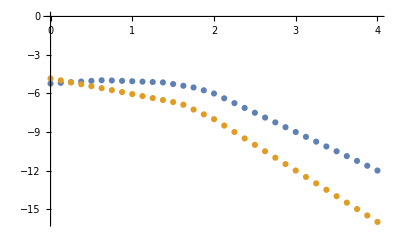

```mathematica
L=6;
EvsV=Table[
eigens = Eigenvalues[NewXXZ[-1.,vv,L,True]];
{vv,Min[eigens]}
,{vv,0,4,0.125}];
EvsV2=Table[
eigens = Eigenvalues[FermionHam[1.,vv,L]];
{vv,Min[eigens]}
,{vv,0,4,0.125}];
ListPlot[{EvsV, EvsV2}]
```

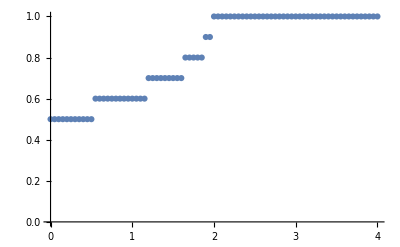

```mathematica
L=8;
nvsV=Table[
{eigs,vecs} = Eigensystem[Chop[NewXXZ[-1.,vv,L,True]]];
gindx= Ordering[eigs][[1]];
gst=vecs[[gindx]];
{vv,Re[gst.Fc[-1,1,L].Fc[+1,1,L].Conjugate[gst]]}
,{vv,0,4,0.05}];
ListPlot[nvsV]
```

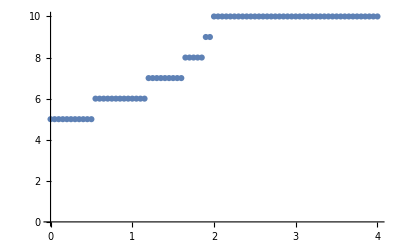

```mathematica
L=8;
TotN=Sum[Fc[-1,kk,L].Fc[+1,kk,L],{kk,1,L}];
NvsV=Table[
{eigs,vecs} = Eigensystem[Chop[NewXXZ[-1.,vv,L,True]]];
gindx= Ordering[eigs][[1]];
gst=vecs[[gindx]];
{vv,Re[gst.TotN.Conjugate[gst]]}
,{vv,0,4,0.05}];
ListPlot[NvsV]
```

```mathematica
L=8;
v=0.914;
TotN=Sum[Fc[+1,kk,L].Fc[-1,kk,L],{kk,1,L}];
(*Ham = Chop[NewXXZ[+1.,v,L,True]];*)
Ham = Chop[FermionHam[+1.,v,L]];
{eigs,vecs} = Eigensystem[Ham];
eigs
(*NvsE=Table[
{Re[vv.Ham.Conjugate[vv]],Re[vv.TotN.Conjugate[vv]]}
,{vv,vecs}];*)
NvsE=Table[
If[Re[vv.TotN.Conjugate[vv]]==3.,Re[vv.Ham.Conjugate[vv]],Nothing]

,{vv,vecs}];

Length[NvsE]
NvsE//Sort
(*
nvsE=Table[
{Re[vv.Ham.Conjugate[vv]],Re[vv.Fc[-1,1,L].Fc[+1,1,L].Conjugate[vv]]}
,{vv,vecs}];

ListPlot[nvsE]*)
```

{-2.914,-2.24151,-2.24151,2.,-2.,-1.828,1.78451,1.78451,1.086,-0.914,-0.914,-0.457,-0.457,1.77636×10^-15,0.,0.}

4

{-2.914,-0.914,-0.914,1.086}

#### Magnetic zero sector GS - Full ED

{{0.0001,0.5},{0.1251,0.5},{0.2501,0.5},{0.3751,0.5},{0.5001,0.5},{0.6251,0.5},{0.7501,0.5},{0.8751,0.5},{1.0001,0.5},{1.1251,0.5},{1.2501,0.5},{1.3751,0.5},{1.5001,0.5},{1.6251,0.5},{1.7501,0.5},{1.8751,0.5},{2.0001,0.5},{2.1251,0.5},{2.2501,0.5},{2.3751,0.5},{2.5001,0.5},{2.6251,0.5},{2.7501,0.5},{2.8751,0.5}}

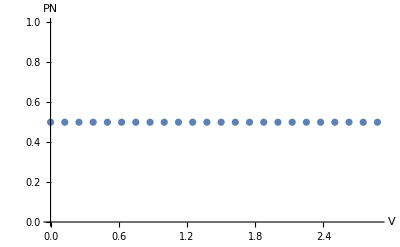

```mathematica
L=4;

TotN=Sum[Fc[+1,kk,L].Fc[-1,kk,L],{kk,1,L}];
N1 = Fc[+1,1,L].Fc[-1,1,L];
data=Table[
Ham=N[FermionHam[1.,Vs,L]];
(*Ham=N[NewXXZ[-1.,-Vs,L,True]];*)
{es, vecs}=Eigensystem[Ham];
EvsV2=Table[
PN = Re[vv.TotN.Conjugate[vv]];
If[Abs[PN-L/2]<=10^-2,
{Re[vv.Ham.Conjugate[vv]],Re[vv.N1.Conjugate[vv]],PN},
Nothing
]
,{vv,vecs}];

(*Print[Sort[EvsV2[[All,1]]]];*)

{Vs, Sort[EvsV2][[1,2]]}

,{Vs,0.0001,3,0.125}]

ListPlot[{EvsV2}, AxesLabel->{"Energy", "PN"}];
ListPlot[data[[All]], AxesLabel->{"V", "PN"}]
```

```mathematica
data[[All,{1,2,1}]];
data;
```

```mathematica
Diagonal[KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]]
Diagonal[KroneckerProduct[PauliMatrix[3],PauliMatrix[3],PauliMatrix[3]]]
Diagonal[KroneckerProduct[PauliMatrix[3],PauliMatrix[3],PauliMatrix[3],PauliMatrix[3]]]
xx = Table[2^l,{l,0,15}]
Accumulate[xx]
yy = Accumulate[Table[l,{l,0,15}]];
Table[(-1)^x,{x,xx}];
Table[(-1)^x,{x,yy}];
(%+1)/2;
%[[1;;8]];
FromDigits[%[[1;;8]],2];
Diagonal[KroneckerProduct[PauliMatrix[3],PauliMatrix[3],PauliMatrix[3],PauliMatrix[3], PauliMatrix[3]]]
```

{1,-1,-1,1}

{1,-1,-1,1,-1,1,1,-1}

{1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,1}

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

{1,3,7,15,31,63,127,255,511,1023,2047,4095,8191,16383,32767,65535}

{1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1}

```mathematica
L=4;
Table[Binomial[L,j],{j,0,L-1}]
Table[Exp[I(2*j-L)*Pi/2]*(-1)^j//ExpToTrig,{j,0,L-1}]
```

{1,4,6,4}

{1,1,1,1}

#### Magnetic zero sector GS - Partial Construction ED

```mathematica
L=4;
{zero,one} ={{1,0},{0,1}};
 
(*config = Table[0,{l,L}]*)
config0 = Table[one,{i,1,L}];
State0=Flatten[KroneckerProduct[Sequence@@config0]];

ham=XXZHamil[1,δ,0,L,True];
State0.ham.State0
(*MatrixForm[ham]*)
Diagonal[ham]
Diagonal[ham,1];
Diagonal[ham,-1];
ham//Flatten//Tally;
```

-2 δ

{-2 δ,0,0,0,0,2 δ,0,0,0,0,2 δ,0,0,0,0,-2 δ}

```mathematica
Table[
select = PadLeft[IntegerDigits[ii,2],L]
,{ii,0,2^L-1}];
Table[
select = PadLeft[IntegerDigits[ii,2],L];
out=-δ/2*(4*(select.RotateLeft[select]-Total[select])+L);
{ii,out}
,{ii,0,2^L-1}]
%/.δ->3.1415;
Table[
{
ii,
select = PadLeft[IntegerDigits[ii,2],L];
select2 = RotateLeft[select];
condi=BitXor[select,select2]
}
,{ii,0,2^L-1}]

BitFlip[list_,n_Integer, m_Integer]:=Module[{lis=list, n0=n, m0=m},
lis[[{n0,m0}]]=Reverse[lis[[{n0,m0}]]];
(*If[lis[[n0]]==1,
lis[[n0]]=0,
lis[[n0]]=1];*)
lis]

BitFlip[{0,0,1,1},2,3];

Table[

select = PadLeft[IntegerDigits[ii,2],L];
select2 = RotateLeft[select];
Table[
If[select[[nn]]!=select2[[nn]],
newselect = BitFlip[select,Mod[nn,L,1],Mod[nn+1,L,1]];
{FromDigits[newselect,2],FromDigits[select,2]}//Reverse,
Nothing(*{0}*)
]
,{nn,1,L}]
,{ii,0,2^L-1}]
%//Flatten//Tally;
```

{{0,-2 δ},{1,0},{2,0},{3,0},{4,0},{5,2 δ},{6,0},{7,0},{8,0},{9,0},{10,2 δ},{11,0},{12,0},{13,0},{14,0},{15,-2 δ}}

{{0,{0,0,0,0}},{1,{0,0,1,1}},{2,{0,1,1,0}},{3,{0,1,0,1}},{4,{1,1,0,0}},{5,{1,1,1,1}},{6,{1,0,1,0}},{7,{1,0,0,1}},{8,{1,0,0,1}},{9,{1,0,1,0}},{10,{1,1,1,1}},{11,{1,1,0,0}},{12,{0,1,0,1}},{13,{0,1,1,0}},{14,{0,0,1,1}},{15,{0,0,0,0}}}

{{},{{1,2},{1,8}},{{2,4},{2,1}},{{3,5},{3,10}},{{4,8},{4,2}},{{5,9},{5,3},{5,6},{5,12}},{{6,10},{6,5}},{{7,11},{7,14}},{{8,4},{8,1}},{{9,5},{9,10}},{{10,6},{10,12},{10,9},{10,3}},{{11,7},{11,13}},{{12,10},{12,5}},{{13,11},{13,14}},{{14,13},{14,7}},{}}

{{0,32},{2,4},{-1,32},{1,4},{8,4},{4,4},{5,8},{3,4},{10,8},{9,4},{6,4},{12,4},{11,4},{7,4},{14,4},{13,4}}

```mathematica
{{1,1,0,0},{1,0,0,1},{0,1,0,1}}

1-BitOr[{1,1,0,0},{1,0,1,0}]
BitXor[{1,1,0,0},{0,1,0,1}]
```

{{1,1,0,0},{1,0,0,1},{0,1,0,1}}

{0,0,0,1}

{1,0,0,1}

```mathematica
Table[Mod[ii,4,1],{ii,1,15}]
```

{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3}

#### Excited State Sup

```mathematica
L=8;
randmat= RandomReal[{0,1},{L,L}];
(*Amat= 0.5*(randmat+Transpose[randmat]);*)
Amat ={{0.2035917,-1.06105515, 0., 0., 0., 0., 0.,-1.06105619},{-1.06105515, 0.3674083,-1.06105619 ,0., 0., 0., 0., 0.},{0.,-1.06105619, 0.2035917,-1.06105515, 0., 0., 0., 0.},{0., 0.,-1.06105515, 0.3674083,-1.06105619 ,0. ,0., 0.},{0., 0., 0.,-1.06105619, 0.2035917,-1.06105515, 0., 0.},{0., 0., 0., 0.,-1.06105515, 0.3674083,-1.06105619, 0.},{0., 0., 0., 0., 0.,-1.06105619, 0.2035917,-1.06105515},{-1.06105619 ,0. ,0. ,0., 0., 0.,-1.06105515, 0.3674083}};(*{{0.13232786,-1.04618452 ,0.,-1.04618452},{-1.04618452, 0.43867214,-1.04618452, 0.},{0.,-1.04618452, 0.13232786,-1.04618452},{-1.04618452, 0.,-1.04618452, 0.43867214}};*)
(*{{0.2855,-1.07016667, 0., 0., 0.,-1.07016667},{-1.07016667, 0.2855,-1.07016667, 0., 0., 0.},{0.,-1.07016667, 0.2855,-1.07016667, 0., 0.},{0., 0.,-1.07016667, 0.2855,-1.07016667, 0.},{0., 0., 0.,-1.07016667, 0.2855,-1.07016667},{-1.07016667, 0., 0., 0.,-1.07016667 ,0.2855}};*)
{aE,aV}=Eigensystem[Amat];
(*{xx,yy}=Partition[Ordering[aE],L/2];*)
xx=Ordering[aE];
aE=aE[[xx]]
aV=aV[[xx]];
(*aV[[2]]=-aV[[2]];
aV[[3]]=-aV[[3]];*)
(*aV[[{4,5}]]=aV[[{5,4}]];
aV[[4]]=-Reverse[aV[[4]]];
aV[[5]]=-Reverse[aV[[5]]];*)
Total[aE[[Flatten[Position[aE,_?Negative]]]]]-0.0*Total[aE]
(*ListPlot[{aE,aE-0.5*Total[aE]}]*)
randHam= Sum[
Amat[[ii,jj]]*Fc[+1,ii,L].Fc[-1,jj,L]
(*-Amat[[ii,jj]]*Fc[-1,ii,L].Fc[+1,jj,L]*)
, {ii,1,L},{jj,1,L}]-0.0*Tr[Amat]* IdentityMatrix[2^L];
{rEE,rVV}=Eigensystem[randHam];
(*ListPlot[rEE];*)
(*rVV.Transpose[Conjugate[rVV]]//Chop*)
XX=Ordering[rEE];
rEE=rEE[[XX]]
rVV=rVV[[XX]];

(*{{3.6030696*^-01,3.4666828*^-01,3.6030696*^-01,3.4666828*^-01,3.6030696*^-01,3.4666828*^-01,3.6030696*^-01,3.4666828*^-01},{4.3385582*^-01,1.0664362*^-01,-2.7458175*^-01,-4.7434284*^-01,-4.3385582*^-01,-1.0664362*^-01,2.7458175*^-01,4.7434284*^-01},{-2.7458175*^-01,-4.7434284*^-01,-4.3385582*^-01,-1.0664362*^-01,2.7458175*^-01,4.7434284*^-01,4.3385582*^-01,1.0664362*^-01},{5.0000000*^-01,-3.1600000*^-06,-5.0000000*^-01,3.1600000*^-06,5.0000000*^-01,-3.1600000*^-06,-5.0000000*^-01,3.1600000*^-06},{3.1600000*^-06,5.0000000*^-01,-3.1600000*^-06,-5.0000000*^-01,3.1600000*^-06,5.0000000*^-01,-3.1600000*^-06,-5.0000000*^-01},{4.8618308*^-01,-3.6307037*^-01,1.3310000*^-05,3.6305084*^-01,-4.8618308*^-01,3.6307037*^-01,-1.3310000*^-05,-3.6305084*^-01},{1.3310000*^-05,3.6305084*^-01,-4.8618308*^-01,3.6307037*^-01,-1.3310000*^-05,-3.6305084*^-01,4.8618308*^-01,-3.6307037*^-01},{3.4666828*^-01,-3.6030696*^-01,3.4666828*^-01,-3.6030696*^-01,3.4666828*^-01,-3.6030696*^-01,3.4666828*^-01,-3.6030696*^-01}};*)
(*{{0.40824829, 0.40824829, 0.40824829, 0.40824829, 0.40824829, 0.40824829},{-0.57474203,-0.23989787, 0.33484416, 0.57474203, 0.23989787,-0.33484416},{0.05481726, 0.52514983, 0.47033257,-0.05481726,-0.52514983,-0.47033257},{-0.,-0.5, 0.5,-0.,-0.5, 0.5},{0.57735027,-0.28867513,-0.28867513, 0.57735027,-0.28867513,-0.28867513},{-0.40824829 ,0.40824829,-0.40824829, 0.40824829,-0.40824829, 0.40824829}};*)
(*{{-0.51793092,-0.48140166,-0.51793092,-0.48140166},{-0.70710678,-0., 0.70710678 ,0.},{-0., 0.70710678, 0.,-0.70710678},{0.48140166,-0.51793092, 0.48140166,-0.51793092}};*)
aV=
Transpose[{{-3.39873555*^-01,4.72019363*^-01,-2.10779917*^-02,-9.33199659*^-16,-5.00000000*^-01,9.13525147*^-03,-5.25994284*^-01,3.66723283*^-01},{-3.66723283*^-01,3.88214542*^-01,3.55025222*^-01,-5.00000000*^-01,9.71875205*^-16,3.28248679*^-01,3.39851976*^-01,-3.39873555*^-01},{-3.39873555*^-01,2.10779917*^-02,4.72019363*^-01,8.93829981*^-16,5.00000000*^-01,-5.25994284*^-01,-9.13525147*^-03,3.66723283*^-01},{-3.66723283*^-01,-3.55025222*^-01,3.88214542*^-01,5.00000000*^-01,-9.48418693*^-16,3.39851976*^-01,-3.28248679*^-01,-3.39873555*^-01},{-3.39873555*^-01,-4.72019363*^-01,2.10779917*^-02,-8.79177066*^-16,-5.00000000*^-01,-9.13525147*^-03,5.25994284*^-01,3.66723283*^-01},{-3.66723283*^-01,-3.88214542*^-01,-3.55025222*^-01,-5.00000000*^-01,9.13432614*^-16,-3.28248679*^-01,-3.39851976*^-01,-3.39873555*^-01},{-3.39873555*^-01,-2.10779917*^-02,-4.72019363*^-01,9.29031448*^-16,5.00000000*^-01,5.25994284*^-01,9.13525147*^-03,3.66723283*^-01},{-3.66723283*^-01,3.55025222*^-01,-3.88214542*^-01,5.00000000*^-01,-8.01754256*^-16,-3.39851976*^-01,3.28248679*^-01,-3.39873555*^-01}}];
(*Transpose[{{0.35355339,-0.49848992,0.03883046,0.17372147,0.46885056,-0.01583674,-0.49974913,0.35355339},{-0.35355339,0.32502832,-0.37994288,-0.46885056,0.17372147,-0.36457427,-0.34217774,0.35355339},{0.35355339,0.03883046,0.49848992,-0.17372147,-0.46885056,-0.49974913,0.01583674,0.35355339},{-0.35355339,-0.37994288,-0.32502832,0.46885056,-0.17372147,-0.34217774,0.36457427,0.35355339},{0.35355339,0.49848992,-0.03883046,0.17372147,0.46885056,0.01583674,0.49974913,0.35355339},{-0.35355339,-0.32502832,0.37994288,-0.46885056,0.17372147,0.36457427,0.34217774,0.35355339},{0.35355339,-0.03883046,-0.49848992,-0.17372147,-0.46885056,0.49974913,-0.01583674,0.35355339},{-0.35355339,0.37994288,0.32502832,0.46885056,-0.17372147,0.34217774,-0.36457427,0.35355339}}];*)
Table[Length[x], {x,aV}]
MatrixForm[aV]//Chop;
```

Full Hamiltonian

```mathematica
"Full Hamiltonian check - V"
Js=-1.;
Vs=1.1;
sets = Subsets[Range[L],{L/2}];
ord =Ordering[Table[Total[aE[[indxs]]],{indxs,sets}]];
sets=sets[[ord]][[All]];
(*Print[sets -1]*)
vac=PadLeft[{1},2^L];
Ham = FermionHam[Js,Vs,L];
Ham1=Table[
 OPL=Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,KK}]];
stateL=OPL.vac;
OPR= Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,QQ}]];
stateR=OPR.vac;

Chop[stateL.Ham.stateR, 10^-5]

,{KK,sets},{QQ,sets}];
MatrixForm[Ham1]
Eigenvalues[Ham1]//Sort
(*"Hamiltonian element check - ED"
Do[
 OPL=Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,sets[[kkk]]}]];
stateL=OPL.vac;
OPR= Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,sets[[qqq]]}]];
stateR=OPR.vac;
(*Chop[stateL.Ham.stateR, 10^-5]*)
(*Chop[stateL.randHam.stateR, 10^-5]*)

Print[sets[[kkk]]-1,",",sets[[qqq]]-1,"--> ",Chop[stateL.Ham.stateR, 10^-5]];
,{kkk,Length[sets]},{qqq,kkk,Length[sets]}];*)
```

Full Hamiltonian check - V

(5.39497 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.302568 | -0.00824989 | -0.00824989 | -0.302568 | -0.00236644 | -0.0867903 | -0.0867903 | 0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.303551 | 0 | 0 | 0 | 0 | 0 | -0.0635574 | -0.00394505 | 0.00394505 | -0.0635574 | 0 | -0.00394505 | 0 | 0.0635574 | -0.0635574 | -0.00394505 | 0 | 0 | 0 | 0 | 0.135925 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0398638 | 0.00108693 | 0.00108693 | 0.0398638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5.47469 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00293362 | -0.107592 | -0.107592 | 0.00293362 | 0.0292489 | -0.00079751 | -0.00079751 | -0.0292489 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0293439 | 0 | 0 | 0 | 0 | -0.00453252 | 0.0730219 | -0.0730219 | -0.00453252 | 0 | -0.0730219 | 0 | -0.00453252 | 0.00453252 | -0.0730219 | 0 | 0 | 0 | 0 | 0 | 0.135925 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0398638 | 0.00108693 | 0.00108693 | 0.0398638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4.26532 | 0 | -0.00056718 | -0.0208016 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.142348 | -0.0654488 | -0.00883563 | 0.00585691 | -0.00818873 | -0.0063196 | 0.131926 | -0.0706192 | 0 | 0 | -0.00412494 | -0.151284 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.159111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00453252 | -0.0730219 | 0 | 0.0635574 | 0 | 0.00394505 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00108693 | 0 | 0.0398638 | 0 | 0 | 0
0 | 0 | 0 | 4.26532 | -0.0208016 | 0.00056718 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00883563 | 0.00585691 | -0.142348 | 0.0654488 | -0.131926 | -0.0706192 | -0.00818873 | 0.0063196 | 0 | 0 | -0.151284 | 0.00412494 | 0 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.159111 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0730219 | 0.00453252 | 0 | -0.00394505 | 0 | 0.0635574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0398638 | 0 | -0.00108693 | 0 | 0 | 0
0 | 0 | -0.00056718 | -0.0208016 | 4.26532 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00228177 | -0.00883563 | 0.0656707 | -0.142348 | -0.0708587 | -0.131926 | -0.00246203 | 0.00818873 | 0 | 0 | -0.193338 | 0 | -0.00412494 | -0.151284 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.159111 | 0 | 0 | 0 | 0.0730219 | -0.00453252 | 0 | 0 | 0.00394505 | 0 | 0.0635574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00108693 | 0 | 0.0398638 | 0 | 0
0 | 0 | -0.0208016 | 0.00056718 | 0 | 4.26532 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0656707 | 0.142348 | 0.00228177 | -0.00883563 | -0.00246203 | -0.00818873 | 0.0708587 | -0.131926 | 0 | 0 | 0 | -0.193338 | -0.151284 | 0.00412494 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.159111 | 0 | 0 | 0.00453252 | 0.0730219 | 0 | 0 | -0.0635574 | 0 | 0.00394505 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0398638 | 0 | -0.00108693 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3.77311 | 0 | -0.0787906 | -0.00489058 | 0.00489058 | -0.0787906 | -0.00365621 | 0.058904 | -0.058904 | -0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.165909 | 0.0045237 | 0.0045237 | 0.165909 | 0 | 0 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0730219 | 0.00453252 | -0.00453252 | 0.0730219 | -0.00394505 | 0.0635574 | -0.0635574 | -0.00394505 | 0.135925 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.77311 | -0.00489058 | 0.0787906 | -0.0787906 | -0.00489058 | -0.058904 | -0.00365621 | 0.00365621 | -0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.193338 | -0.165909 | 0 | 0.0045237 | 0.0045237 | 0.165909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00453252 | -0.0730219 | 0.0730219 | 0.00453252 | -0.0635574 | -0.00394505 | 0.00394505 | -0.0635574 | 0 | 0.135925 | 0 | 0 | 0 | 0 | 0 | 0
0.302568 | -0.00293362 | 0 | 0 | 0 | 0 | -0.0787906 | -0.00489058 | 2.81047 | 0.00370341 | 0.00370341 | 0.135824 | 0 | -0.0966689 | -0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.234246 | 0 | 0 | 0 | 0 | 0 | -0.141478 | -0.00246203 | 0.0063196 | 0 | 0.00818873 | -0.00878163 | 0.131926 | 0.0708587 | -0.0706192 | 0 | 0 | 0 | 0 | 0 | -0.273319 | 0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.288879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0635574 | 0.00394505 | 0 | 0 | 0 | 0 | 0.0398638 | 0
-0.00824989 | -0.107592 | 0 | 0 | 0 | 0 | -0.00489058 | 0.0787906 | 0.00370341 | 2.9462 | -0.000100978 | -0.00370341 | 0.0966689 | 0 | 0 | -0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00638699 | 0 | 0 | 0 | 0 | 0 | -0.00246203 | 0.000239442 | 0 | 0.0063196 | -0.131926 | 0.0708587 | 0.00818873 | -0.00385756 | 0 | -0.0706192 | 0 | 0 | 0 | 0 | 0.00745238 | 0.0867903 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.288879 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00394505 | -0.0635574 | 0 | 0 | 0 | 0 | -0.00108693 | 0
-0.00824989 | -0.107592 | 0 | 0 | 0 | 0 | 0.00489058 | -0.0787906 | 0.00370341 | -0.000100978 | 2.9462 | -0.00370341 | 0.0966689 | 0 | 0 | -0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00638699 | 0 | 0 | 0 | 0 | 0 | 0.0063196 | 0 | -0.000239442 | -0.00246203 | 0.131926 | -0.0706192 | -0.00818873 | 0 | 0.00385756 | 0.0708587 | 0 | 0 | 0 | 0 | 0.00745238 | 0.0867903 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.288879 | 0 | 0 | 0 | 0 | 0 | -0.00394505 | 0.0635574 | 0 | 0 | 0 | 0 | -0.00108693 | 0
-0.302568 | 0.00293362 | 0 | 0 | 0 | 0 | -0.0787906 | -0.00489058 | 0.135824 | -0.00370341 | -0.00370341 | 2.81047 | 0 | 0.0966689 | 0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0063196 | -0.00246203 | 0.141478 | 0.00818873 | 0 | 0.131926 | -0.0706192 | 0.0708587 | 0.00878163 | 0 | 0 | 0 | 0 | 0.273319 | -0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.288879 | 0 | 0 | 0 | 0 | 0.0635574 | 0.00394505 | 0 | 0 | 0 | 0 | -0.0398638 | 0
-0.00236644 | 0.0292489 | 0 | 0 | 0 | 0 | -0.00365621 | -0.058904 | 0 | 0.0966689 | 0.0966689 | 0 | 2.83134 | 0.00370341 | 0.00370341 | 0.135824 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.234246 | 0 | 0 | 0 | 0 | 0.00813868 | -0.0656707 | 0.0654488 | 0 | 0.142348 | 0.13112 | 0.00883563 | 0.00228177 | -0.00585691 | 0 | 0 | 0 | 0 | 0 | 0.00293362 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.014672 | 0 | 0 | 0 | 0.00453252 | 0.0730219 | 0 | 0 | 0 | 0 | 0 | 0.0398638
-0.0867903 | -0.00079751 | 0 | 0 | 0 | 0 | 0.058904 | -0.00365621 | -0.0966689 | 0 | 0 | 0.0966689 | 0.00370341 | 2.96707 | -0.000100978 | -0.00370341 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00638699 | 0 | 0 | 0 | 0 | -0.0656707 | 0.00357513 | 0 | 0.0654488 | 0.00883563 | 0.00228177 | -0.142348 | -0.000221911 | 0 | -0.00585691 | 0 | 0 | 0 | 0 | 0.107592 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.014672 | 0 | 0 | -0.0730219 | 0.00453252 | 0 | 0 | 0 | 0 | 0 | -0.00108693
-0.0867903 | -0.00079751 | 0 | 0 | 0 | 0 | -0.058904 | 0.00365621 | -0.0966689 | 0 | 0 | 0.0966689 | 0.00370341 | -0.000100978 | 2.96707 | -0.00370341 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00638699 | 0 | 0 | 0 | 0 | 0.0654488 | 0 | -0.00357513 | -0.0656707 | -0.00883563 | -0.00585691 | 0.142348 | 0 | 0.000221911 | 0.00228177 | 0 | 0 | 0 | 0 | 0.107592 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.014672 | 0 | 0.0730219 | -0.00453252 | 0 | 0 | 0 | 0 | 0 | -0.00108693
0.00236644 | -0.0292489 | 0 | 0 | 0 | 0 | -0.00365621 | -0.058904 | 0 | -0.0966689 | -0.0966689 | 0 | 0.135824 | -0.00370341 | -0.00370341 | 2.83134 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0.0654488 | -0.0656707 | -0.00813868 | 0.142348 | 0 | 0.00883563 | -0.00585691 | 0.00228177 | -0.13112 | 0 | 0 | 0 | 0 | -0.00293362 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.014672 | 0.00453252 | 0.0730219 | 0 | 0 | 0 | 0 | 0 | -0.0398638
0 | 0 | -0.142348 | 0.00883563 | -0.00228177 | 0.0656707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.35388 | -0.194382 | 0 | 0.00530006 | 0 | 0 | -0.0966689 | 0 | 0 | 0 | 0 | 0 | 0.058904 | -0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.131926 | -0.00818873 | -0.00246203 | 0.0708587 | 0 | 0 | 0.00785113 | 0.287944 | 0 | 0 | 0.0867903 | 0 | -0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0635574 | 0 | -0.00394505 | 0 | 0
0 | 0 | -0.0654488 | 0.00585691 | -0.00883563 | 0.142348 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.194382 | 2.35388 | 0.00530006 | 0 | 0 | 0 | 0 | -0.0966689 | 0 | 0 | 0.00365621 | -0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0706192 | 0.0063196 | 0.00818873 | -0.131926 | 0 | 0 | 0 | 0 | 0.00785113 | 0.287944 | 0 | 0.0867903 | 0 | -0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00394505 | 0 | -0.0635574 | 0 | 0 | 0
0 | 0 | -0.00883563 | -0.142348 | 0.0656707 | 0.00228177 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00530006 | 2.35388 | 0.194382 | 0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00365621 | 0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00818873 | 0.131926 | 0.0708587 | 0.00246203 | 0 | 0 | 0.287944 | -0.00785113 | 0 | 0 | -0.00236644 | 0 | -0.0867903 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00394505 | 0 | 0.0635574 | 0 | 0
0 | 0 | 0.00585691 | 0.0654488 | -0.142348 | -0.00883563 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00530006 | 0 | 0.194382 | 2.35388 | 0 | 0.0966689 | 0 | 0 | 0 | 0 | 0.058904 | 0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0063196 | 0.0706192 | 0.131926 | 0.00818873 | 0 | 0 | 0 | 0 | 0.287944 | -0.00785113 | 0 | -0.00236644 | 0 | -0.0867903 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0635574 | 0 | 0.00394505 | 0 | 0 | 0
0 | 0 | -0.00818873 | -0.131926 | -0.0708587 | -0.00246203 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0966689 | 0 | 2.38331 | -0.194382 | 0 | 0.00530006 | 0 | 0 | 0 | 0 | 0.00489058 | 0.0787906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00883563 | -0.142348 | 0.0656707 | 0.00228177 | 0 | 0 | 0.107592 | -0.00293362 | 0 | 0 | 0.000398755 | 0 | 0.0146245 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00453252 | 0 | -0.0730219 | 0 | 0
0 | 0 | -0.0063196 | -0.0706192 | -0.131926 | -0.00818873 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0966689 | -0.194382 | 2.38331 | 0.00530006 | 0 | 0 | 0 | 0.0787906 | 0.00489058 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00585691 | 0.0654488 | -0.142348 | -0.00883563 | 0 | 0 | 0 | 0 | 0.107592 | -0.00293362 | 0 | 0.000398755 | 0 | 0.0146245 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0730219 | 0 | -0.00453252 | 0 | 0 | 0
0 | 0 | 0.131926 | -0.00818873 | -0.00246203 | 0.0708587 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0966689 | 0 | 0 | 0 | 0 | 0.00530006 | 2.38331 | 0.194382 | 0 | 0 | 0 | 0 | -0.0787906 | 0.00489058 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.142348 | -0.00883563 | 0.00228177 | -0.0656707 | 0 | 0 | -0.00293362 | -0.107592 | 0 | 0 | 0.0146245 | 0 | -0.000398755 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0730219 | 0 | -0.00453252 | 0 | 0
0 | 0 | -0.0706192 | 0.0063196 | 0.00818873 | -0.131926 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0966689 | 0 | 0 | 0.00530006 | 0 | 0.194382 | 2.38331 | 0 | 0 | -0.00489058 | 0.0787906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0654488 | -0.00585691 | 0.00883563 | -0.142348 | 0 | 0 | 0 | 0 | -0.00293362 | -0.107592 | 0 | 0.0146245 | 0 | -0.000398755 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00453252 | 0 | -0.0730219 | 0 | 0 | 0
0.303551 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.234246 | 0.00638699 | 0.00638699 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.8174 | 0 | 0 | 0 | 0 | 0 | 0.058904 | 0.00365621 | -0.00365621 | 0.058904 | 0 | 0.00365621 | 0 | -0.058904 | 0.058904 | 0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.302568 | -0.00824988 | -0.00824988 | -0.302568 | -0.00236644 | -0.0867903 | -0.0867903 | 0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0.135925 | 0
0 | 0.0293439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.234246 | 0.00638699 | 0.00638699 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.85539 | 0 | 0 | 0 | 0 | -0.00489058 | 0.0787906 | -0.0787906 | -0.00489058 | 0 | -0.0787906 | 0 | -0.00489058 | 0.00489058 | -0.0787906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00293362 | -0.107592 | -0.107592 | 0.00293362 | 0.0292489 | -0.000797508 | -0.000797508 | -0.0292489 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.135925
0 | 0 | -0.00412494 | -0.151284 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00365621 | 0 | 0.058904 | 0 | 0.0787906 | 0 | -0.00489058 | 0 | 0 | 1.64815 | 0 | 0.00056718 | 0.0208016 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00638699 | 0.234246 | 0 | 0 | 0 | 0 | 0.142348 | -0.00883563 | 0.0656707 | 0.00228177 | 0.00818873 | 0.00246203 | 0.131926 | -0.0708587 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.144439 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.151284 | 0.00412494 | 0 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.058904 | 0 | 0.00365621 | 0 | 0.00489058 | 0 | 0.0787906 | 0 | 0 | 0 | 1.64815 | 0.0208016 | -0.00056718 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.234246 | -0.00638699 | 0 | 0 | 0 | 0 | 0.00883563 | 0.142348 | 0.00228177 | -0.0656707 | -0.131926 | -0.0708587 | 0.00818873 | -0.00246203 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.144439 | 0 | 0 | 0
0 | 0 | -0.193338 | 0 | -0.00412494 | -0.151284 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.058904 | 0 | 0.00365621 | 0 | 0.00489058 | 0 | -0.0787906 | 0 | 0 | 0 | 0.00056718 | 0.0208016 | 1.64815 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00638699 | 0.234246 | 0 | 0 | 0.00585691 | 0.0654488 | 0.00883563 | -0.142348 | 0.0706192 | 0.131926 | -0.0063196 | 0.00818873 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.144439 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.193338 | -0.151284 | 0.00412494 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00365621 | 0 | 0.058904 | 0 | 0.0787906 | 0 | 0.00489058 | 0 | 0 | 0 | 0.0208016 | -0.00056718 | 0 | 1.64815 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.234246 | -0.00638699 | 0 | 0 | 0.0654488 | -0.00585691 | 0.142348 | 0.00883563 | -0.0063196 | -0.00818873 | -0.0706192 | 0.131926 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.144439 | 0 | 0
-0.0635574 | -0.00453252 | 0 | 0 | 0 | 0 | -0.165909 | 0 | -0.141478 | -0.00246203 | 0.0063196 | 0 | 0.00813868 | -0.0656707 | 0.0654488 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.058904 | -0.00489058 | 0 | 0 | 0 | 0 | 0.964176 | 0.00370341 | 0.00370341 | 0.135824 | 0.00530006 | 0 | 0.0208016 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0787906 | 0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.13112 | 0.00228177 | -0.00585691 | 0 | 0.00878163 | -0.0708587 | 0.0706192 | 0 | 0.13666 | 0 | 0 | 0 | 0 | 0 | -0.0730219 | 0.00394505
-0.00394505 | 0.0730219 | 0 | 0 | 0 | 0 | 0.0045237 | 0 | -0.00246203 | 0.000239442 | 0 | 0.0063196 | -0.0656707 | 0.00357513 | 0 | 0.0654488 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00365621 | 0.0787906 | 0 | 0 | 0 | 0 | 0.00370341 | 1.0999 | -0.000100978 | -0.00370341 | 0.194382 | 0 | -0.00056718 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00489058 | -0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00228177 | -0.000221911 | 0 | -0.00585691 | -0.0708587 | 0.00385756 | 0 | 0.0706192 | -0.00372619 | 0 | 0 | 0 | 0 | 0 | -0.00453252 | -0.0635574
0.00394505 | -0.0730219 | 0 | 0 | 0 | 0 | 0.0045237 | 0 | 0.0063196 | 0 | -0.000239442 | -0.00246203 | 0.0654488 | 0 | -0.00357513 | -0.0656707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00365621 | -0.0787906 | 0 | 0 | 0 | 0 | 0.00370341 | -0.000100978 | 1.0999 | -0.00370341 | 0.194382 | 0 | -0.00056718 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00489058 | 0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00585691 | 0 | 0.000221911 | 0.00228177 | 0.0706192 | 0 | -0.00385756 | -0.0708587 | -0.00372619 | 0 | 0 | 0 | 0 | 0 | 0.00453252 | 0.0635574
-0.0635574 | -0.00453252 | 0 | 0 | 0 | 0 | 0.165909 | 0 | 0 | 0.0063196 | -0.00246203 | 0.141478 | 0 | 0.0654488 | -0.0656707 | -0.00813868 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.058904 | -0.00489058 | 0 | 0 | 0 | 0 | 0.135824 | -0.00370341 | -0.00370341 | 0.964176 | -0.00530006 | 0 | -0.0208016 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0787906 | 0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00585691 | 0.00228177 | -0.13112 | 0 | 0.0706192 | -0.0708587 | -0.00878163 | -0.13666 | 0 | 0 | 0 | 0 | 0 | -0.0730219 | 0.00394505
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.193338 | 0.00818873 | -0.131926 | 0.131926 | 0.00818873 | 0.142348 | 0.00883563 | -0.00883563 | 0.142348 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00530006 | 0.194382 | 0.194382 | -0.00530006 | 1.1 | 0.0208016 | 0 | -0.00056718 | -0.00056718 | -0.0208016 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00883563 | -0.142348 | 0.142348 | 0.00883563 | -0.131926 | -0.00818873 | 0.00818873 | -0.131926 | 0 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0
-0.00394505 | -0.0730219 | 0 | 0 | 0 | 0 | 0 | -0.165909 | -0.00878163 | 0.0708587 | -0.0706192 | 0 | 0.13112 | 0.00228177 | -0.00585691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00365621 | -0.0787906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0208016 | 0.964176 | 0.00530006 | 0.00370341 | 0.00370341 | 0.135824 | 0 | 0 | 0 | 0 | 0.00489058 | 0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00813868 | -0.0656707 | 0.0654488 | 0 | 0.141478 | 0.00246203 | -0.0063196 | 0 | 0 | 0.13666 | 0 | 0 | 0 | 0 | -0.00453252 | 0.0635574
0 | 0 | 0 | 0 | 0 | 0 | -0.193338 | 0 | 0.131926 | 0.00818873 | -0.00818873 | 0.131926 | 0.00883563 | -0.142348 | 0.142348 | 0.00883563 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0208016 | -0.00056718 | -0.00056718 | -0.0208016 | 0 | 0.00530006 | 1.1 | 0.194382 | 0.194382 | -0.00530006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.142348 | 0.00883563 | -0.00883563 | 0.142348 | -0.00818873 | 0.131926 | -0.131926 | -0.00818873 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0635574 | -0.00453252 | 0 | 0 | 0 | 0 | 0 | 0.0045237 | 0.0708587 | -0.00385756 | 0 | -0.0706192 | 0.00228177 | -0.000221911 | 0 | -0.00585691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.058904 | -0.00489058 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00056718 | 0.00370341 | 0.194382 | 1.0999 | -0.000100978 | -0.00370341 | 0 | 0 | 0 | 0 | -0.0787906 | 0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0656707 | 0.00357513 | 0 | 0.0654488 | 0.00246203 | -0.000239442 | 0 | -0.0063196 | 0 | -0.00372619 | 0 | 0 | 0 | 0 | 0.0730219 | 0.00394505
-0.0635574 | 0.00453252 | 0 | 0 | 0 | 0 | 0 | 0.0045237 | -0.0706192 | 0 | 0.00385756 | 0.0708587 | -0.00585691 | 0 | 0.000221911 | 0.00228177 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.058904 | 0.00489058 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00056718 | 0.00370341 | 0.194382 | -0.000100978 | 1.0999 | -0.00370341 | 0 | 0 | 0 | 0 | 0.0787906 | -0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0654488 | 0 | -0.00357513 | -0.0656707 | -0.0063196 | 0 | 0.000239442 | 0.00246203 | 0 | -0.00372619 | 0 | 0 | 0 | 0 | -0.0730219 | -0.00394505
-0.00394505 | -0.0730219 | 0 | 0 | 0 | 0 | 0 | 0.165909 | 0 | -0.0706192 | 0.0708587 | 0.00878163 | 0 | -0.00585691 | 0.00228177 | -0.13112 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00365621 | -0.0787906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0208016 | 0.135824 | -0.00530006 | -0.00370341 | -0.00370341 | 0.964176 | 0 | 0 | 0 | 0 | 0.00489058 | 0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0654488 | -0.0656707 | -0.00813868 | 0 | -0.0063196 | 0.00246203 | -0.141478 | 0 | -0.13666 | 0 | 0 | 0 | 0 | -0.00453252 | 0.0635574
0 | 0 | 0.159111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.131926 | -0.0706192 | 0.00818873 | 0.0063196 | -0.00883563 | 0.00585691 | 0.142348 | 0.0654488 | 0 | 0 | 0.00638699 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.471867 | 0 | -0.00056718 | -0.0208016 | 0 | 0 | 0 | 0 | 0.00489058 | -0.0787906 | 0 | -0.058904 | 0 | -0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00412494 | -0.193338 | -0.151284 | 0 | 0 | 0
0 | 0 | 0 | 0.159111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00818873 | 0.0063196 | 0.131926 | 0.0706192 | -0.142348 | 0.0654488 | -0.00883563 | -0.00585691 | 0 | 0 | 0.234246 | -0.00638699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.471867 | -0.0208016 | 0.00056718 | 0 | 0 | 0 | 0 | 0.0787906 | 0.00489058 | 0 | 0.00365621 | 0 | -0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.151284 | 0 | 0.00412494 | -0.193338 | 0 | 0
0 | 0 | 0 | 0 | 0.159111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00246203 | 0.00818873 | 0.0708587 | 0.131926 | 0.0656707 | -0.142348 | 0.00228177 | 0.00883563 | 0 | 0 | 0 | 0 | 0.00638699 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00056718 | -0.0208016 | 0.471867 | 0 | 0 | 0 | 0.0787906 | -0.00489058 | 0 | 0 | -0.00365621 | 0 | -0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.193338 | -0.00412494 | 0 | -0.151284 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.159111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0708587 | -0.131926 | 0.00246203 | 0.00818873 | 0.00228177 | -0.00883563 | -0.0656707 | -0.142348 | 0 | 0 | 0 | 0 | 0.234246 | -0.00638699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0208016 | 0.00056718 | 0 | 0.471867 | 0 | 0 | 0.00489058 | 0.0787906 | 0 | 0 | 0.058904 | 0 | -0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.151284 | -0.193338 | 0.00412494 | 0 | 0
0.135925 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.273319 | 0.00745238 | 0.00745238 | 0.273319 | 0.00293362 | 0.107592 | 0.107592 | -0.00293362 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0787906 | 0.00489058 | -0.00489058 | 0.0787906 | 0 | 0.00489058 | 0 | -0.0787906 | 0.0787906 | 0.00489058 | 0 | 0 | 0 | 0 | 0.219481 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.234246 | -0.00638699 | -0.00638699 | -0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.274207 | 0
0 | 0.135925 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00236644 | 0.0867903 | 0.0867903 | -0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00365621 | -0.058904 | 0.058904 | 0.00365621 | 0 | 0.058904 | 0 | 0.00365621 | -0.00365621 | 0.058904 | 0 | 0 | 0 | 0 | 0 | 0.181492 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.234246 | -0.00638699 | -0.00638699 | -0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0730219 | 0.00453252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00785113 | 0 | 0.287944 | 0 | 0.107592 | 0 | -0.00293362 | 0 | 0 | 0 | 0.142348 | 0.00883563 | 0.00585691 | 0.0654488 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0787906 | 0.00489058 | 0 | 0 | -0.428878 | 0 | 0.194382 | -0.00530006 | 0 | 0 | -0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.131926 | 0.0063196 | -0.00818873 | 0.0706192 | 0 | 0
0 | 0 | 0 | 0 | -0.00453252 | 0.0730219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.287944 | 0 | -0.00785113 | 0 | -0.00293362 | 0 | -0.107592 | 0 | 0 | 0 | -0.00883563 | 0.142348 | 0.0654488 | -0.00585691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00489058 | 0.0787906 | 0 | 0 | 0 | -0.428878 | -0.00530006 | -0.194382 | 0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00818873 | 0.0706192 | -0.131926 | -0.0063196 | 0 | 0
0 | 0 | 0.00453252 | 0.0730219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00785113 | 0 | 0.287944 | 0 | 0.107592 | 0 | -0.00293362 | 0 | 0 | 0.0656707 | 0.00228177 | 0.00883563 | 0.142348 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00489058 | 0.0787906 | 0 | 0 | 0 | 0 | 0.194382 | -0.00530006 | -0.428878 | 0 | 0 | 0 | 0 | -0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0708587 | -0.00818873 | 0.00246203 | -0.131926 | 0 | 0
0 | 0 | -0.0730219 | 0.00453252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.287944 | 0 | -0.00785113 | 0 | -0.00293362 | 0 | -0.107592 | 0 | 0 | 0.00228177 | -0.0656707 | -0.142348 | 0.00883563 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0787906 | 0.00489058 | 0 | 0 | 0 | 0 | -0.00530006 | -0.194382 | 0 | -0.428878 | 0 | 0.0966689 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00246203 | 0.131926 | -0.0708587 | -0.00818873 | 0 | 0
0 | 0 | 0 | 0 | 0.00394505 | -0.0635574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0867903 | 0 | -0.00236644 | 0 | 0.000398755 | 0 | 0.0146245 | 0 | 0 | 0 | 0.00818873 | -0.131926 | 0.0706192 | -0.0063196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00365621 | 0.058904 | 0 | 0 | 0 | 0.0966689 | 0 | 0 | -0.458307 | 0.194382 | 0 | -0.00530006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00883563 | -0.0654488 | -0.142348 | 0.00585691 | 0 | 0
0 | 0 | 0.0635574 | -0.00394505 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0867903 | 0 | -0.00236644 | 0 | 0.000398755 | 0 | 0.0146245 | 0 | 0 | 0.00246203 | -0.0708587 | 0.131926 | -0.00818873 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.058904 | 0.00365621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0966689 | 0.194382 | -0.458307 | -0.00530006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00228177 | 0.142348 | 0.0656707 | -0.00883563 | 0 | 0
0 | 0 | 0 | 0 | 0.0635574 | 0.00394505 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00236644 | 0 | -0.0867903 | 0 | 0.0146245 | 0 | -0.000398755 | 0 | 0 | 0 | 0.131926 | 0.00818873 | -0.0063196 | -0.0706192 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.058904 | -0.00365621 | 0 | 0 | -0.0966689 | 0 | 0 | 0 | 0 | -0.00530006 | -0.458307 | -0.194382 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.142348 | 0.00585691 | 0.00883563 | 0.0654488 | 0 | 0
0 | 0 | 0.00394505 | 0.0635574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00236644 | 0 | -0.0867903 | 0 | 0.0146245 | 0 | -0.000398755 | 0 | 0 | -0.0708587 | -0.00246203 | 0.00818873 | 0.131926 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00365621 | -0.058904 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0966689 | 0 | -0.00530006 | 0 | -0.194382 | -0.458307 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0656707 | 0.00883563 | 0.00228177 | 0.142348 | 0 | 0
-0.0398638 | 0 | 0 | 0 | 0 | 0 | 0.0730219 | 0.00453252 | 0.288879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.302568 | -0.00293362 | 0 | 0 | 0 | 0 | 0.13112 | 0.00228177 | -0.00585691 | 0 | 0.00883563 | 0.00813868 | 0.142348 | -0.0656707 | 0.0654488 | 0 | 0 | 0 | 0 | 0 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.15712 | 0.00370341 | 0.00370341 | 0.135824 | 0 | -0.0966689 | -0.0966689 | 0 | -0.058904 | -0.00365621 | 0 | 0 | 0 | 0 | -0.273319 | 0.00236644
0.00108693 | 0 | 0 | 0 | 0 | 0 | 0.00453252 | -0.0730219 | 0 | 0.288879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00824988 | -0.107592 | 0 | 0 | 0 | 0 | 0.00228177 | -0.000221911 | 0 | -0.00585691 | -0.142348 | -0.0656707 | 0.00883563 | 0.00357513 | 0 | 0.0654488 | 0 | 0 | 0 | 0 | -0.00638699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00370341 | -1.0214 | -0.000100978 | -0.00370341 | 0.0966689 | 0 | 0 | -0.0966689 | -0.00365621 | 0.058904 | 0 | 0 | 0 | 0 | 0.00745238 | 0.0867903
0.00108693 | 0 | 0 | 0 | 0 | 0 | -0.00453252 | 0.0730219 | 0 | 0 | 0.288879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00824988 | -0.107592 | 0 | 0 | 0 | 0 | -0.00585691 | 0 | 0.000221911 | 0.00228177 | 0.142348 | 0.0654488 | -0.00883563 | 0 | -0.00357513 | -0.0656707 | 0 | 0 | 0 | 0 | -0.00638699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00370341 | -0.000100978 | -1.0214 | -0.00370341 | 0.0966689 | 0 | 0 | -0.0966689 | 0.00365621 | -0.058904 | 0 | 0 | 0 | 0 | 0.00745238 | 0.0867903
0.0398638 | 0 | 0 | 0 | 0 | 0 | 0.0730219 | 0.00453252 | 0 | 0 | 0 | 0.288879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.302568 | 0.00293362 | 0 | 0 | 0 | 0 | 0 | -0.00585691 | 0.00228177 | -0.13112 | 0.00883563 | 0 | 0.142348 | 0.0654488 | -0.0656707 | -0.00813868 | 0 | 0 | 0 | 0 | -0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.135824 | -0.00370341 | -0.00370341 | -1.15712 | 0 | 0.0966689 | 0.0966689 | 0 | -0.058904 | -0.00365621 | 0 | 0 | 0 | 0 | 0.273319 | -0.00236644
0 | -0.0398638 | 0 | 0 | 0 | 0 | -0.00394505 | -0.0635574 | 0 | 0 | 0 | 0 | 0.014672 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00236644 | 0.0292489 | 0 | 0 | 0 | 0 | 0.00878163 | -0.0708587 | 0.0706192 | 0 | -0.131926 | 0.141478 | -0.00818873 | 0.00246203 | -0.0063196 | 0 | 0 | 0 | 0 | 0 | 0 | 0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0966689 | 0.0966689 | 0 | -1.17799 | 0.00370341 | 0.00370341 | 0.135824 | 0.00489058 | 0.0787906 | 0 | 0 | 0 | 0 | 0.00293362 | 0
0 | 0.00108693 | 0 | 0 | 0 | 0 | 0.0635574 | -0.00394505 | 0 | 0 | 0 | 0 | 0 | 0.014672 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0867903 | -0.000797508 | 0 | 0 | 0 | 0 | -0.0708587 | 0.00385756 | 0 | 0.0706192 | -0.00818873 | 0.00246203 | 0.131926 | -0.000239442 | 0 | -0.0063196 | 0 | 0 | 0 | 0 | 0 | -0.00638699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0966689 | 0 | 0 | 0.0966689 | 0.00370341 | -1.04227 | -0.000100978 | -0.00370341 | -0.0787906 | 0.00489058 | 0 | 0 | 0 | 0 | 0.107592 | 0
0 | 0.00108693 | 0 | 0 | 0 | 0 | -0.0635574 | 0.00394505 | 0 | 0 | 0 | 0 | 0 | 0 | 0.014672 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0867903 | -0.000797508 | 0 | 0 | 0 | 0 | 0.0706192 | 0 | -0.00385756 | -0.0708587 | 0.00818873 | -0.0063196 | -0.131926 | 0 | 0.000239442 | 0.00246203 | 0 | 0 | 0 | 0 | 0 | -0.00638699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0966689 | 0 | 0 | 0.0966689 | 0.00370341 | -0.000100978 | -1.04227 | -0.00370341 | 0.0787906 | -0.00489058 | 0 | 0 | 0 | 0 | 0.107592 | 0
0 | 0.0398638 | 0 | 0 | 0 | 0 | -0.00394505 | -0.0635574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.014672 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00236644 | -0.0292489 | 0 | 0 | 0 | 0 | 0 | 0.0706192 | -0.0708587 | -0.00878163 | -0.131926 | 0 | -0.00818873 | -0.0063196 | 0.00246203 | -0.141478 | 0 | 0 | 0 | 0 | 0 | -0.234246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0966689 | -0.0966689 | 0 | 0.135824 | -0.00370341 | -0.00370341 | -1.17799 | 0.00489058 | 0.0787906 | 0 | 0 | 0 | 0 | -0.00293362 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.135925 | 0 | 0.0635574 | 0.00394505 | -0.00394505 | 0.0635574 | 0.00453252 | -0.0730219 | 0.0730219 | 0.00453252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.13666 | -0.00372619 | -0.00372619 | -0.13666 | 0 | 0 | -0.193338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.058904 | -0.00365621 | 0.00365621 | -0.058904 | 0.00489058 | -0.0787906 | 0.0787906 | 0.00489058 | -1.85126 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.135925 | 0.00394505 | -0.0635574 | 0.0635574 | 0.00394505 | 0.0730219 | 0.00453252 | -0.00453252 | 0.0730219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.193338 | 0.13666 | 0 | -0.00372619 | -0.00372619 | -0.13666 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00365621 | 0.058904 | -0.058904 | -0.00365621 | 0.0787906 | 0.00489058 | -0.00489058 | 0.0787906 | 0 | -1.85126 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.00108693 | 0.0398638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00394505 | 0 | 0.0635574 | 0 | -0.0730219 | 0 | 0.00453252 | 0 | 0 | 0.144439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00412494 | -0.151284 | -0.193338 | 0 | 0 | 0 | -0.131926 | 0.00818873 | 0.0708587 | 0.00246203 | 0.00883563 | -0.00228177 | 0.142348 | 0.0656707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.53533 | 0.00056718 | 0 | 0.0208016 | 0 | 0
0 | 0 | 0 | 0 | 0.00108693 | 0.0398638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0635574 | 0 | 0.00394505 | 0 | -0.00453252 | 0 | 0.0730219 | 0 | 0 | 0 | 0 | 0 | 0.144439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.193338 | 0 | -0.00412494 | -0.151284 | 0 | 0 | 0.0063196 | 0.0706192 | -0.00818873 | 0.131926 | -0.0654488 | 0.142348 | 0.00585691 | 0.00883563 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00056718 | -2.53533 | 0.0208016 | 0 | 0 | 0
0 | 0 | 0.0398638 | -0.00108693 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0635574 | 0 | 0.00394505 | 0 | -0.00453252 | 0 | -0.0730219 | 0 | 0 | 0 | 0.144439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.151284 | 0.00412494 | 0 | -0.193338 | 0 | 0 | -0.00818873 | -0.131926 | 0.00246203 | -0.0708587 | -0.142348 | 0.0656707 | 0.00883563 | 0.00228177 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0208016 | -2.53533 | -0.00056718 | 0 | 0
0 | 0 | 0 | 0 | 0.0398638 | -0.00108693 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00394505 | 0 | 0.0635574 | 0 | -0.0730219 | 0 | -0.00453252 | 0 | 0 | 0 | 0 | 0 | 0 | 0.144439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.193338 | -0.151284 | 0.00412494 | 0 | 0 | 0.0706192 | -0.0063196 | -0.131926 | -0.00818873 | 0.00585691 | -0.00883563 | 0.0654488 | 0.142348 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0208016 | 0 | -0.00056718 | -2.53533 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0398638 | -0.00108693 | -0.00108693 | -0.0398638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.135925 | 0 | 0 | 0 | 0 | 0 | -0.0730219 | -0.00453252 | 0.00453252 | -0.0730219 | 0 | -0.00453252 | 0 | 0.0730219 | -0.0730219 | -0.00453252 | 0 | 0 | 0 | 0 | 0.274207 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.273319 | 0.00745238 | 0.00745238 | 0.273319 | 0.00293362 | 0.107592 | 0.107592 | -0.00293362 | 0 | 0 | 0 | 0 | 0 | 0 | -4.13814 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0398638 | -0.00108693 | -0.00108693 | -0.0398638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.135925 | 0 | 0 | 0 | 0 | 0.00394505 | -0.0635574 | 0.0635574 | 0.00394505 | 0 | 0.0635574 | 0 | 0.00394505 | -0.00394505 | 0.0635574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00236644 | 0.0867903 | 0.0867903 | -0.00236644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.21787)

{-4.22971,-4.22971,-2.58625,-2.58625,-2.58625,-2.58625,-1.90573,-1.90573,-1.48194,-1.48194,-1.06371,-1.06371,-1.06371,-1.06371,-0.961215,-0.961215,-0.670337,-0.670337,-0.670337,-0.670337,-0.266685,-0.266685,-0.266685,-0.266685,0.213875,0.213875,0.430137,0.430137,0.430137,0.430137,0.830101,0.830101,0.830101,0.830101,1.1,1.1,1.1,1.1,1.36728,1.36728,1.68595,1.68595,1.68595,1.68595,1.75798,1.75798,2.15865,2.15865,2.15865,2.15865,2.62794,2.62794,2.62794,2.62794,2.70935,2.70935,2.98361,2.98361,2.98361,2.98361,3.09907,3.09907,3.83845,3.83845,4.32059,4.32059,4.32059,4.32059,5.49258,5.49258}

```mathematica
Pham=StringReplace["",{ " "..->","}];
StringReplace[%,{"[[,"->"{{","]]"->"}}","],["->"},{"}];
StringReplace[%,{"{,0."->"{0.","0.,}"->"0.}"}];
(*StringReplace[%,{",},{"->"},{","0.,}"->"0.}"}]*)
ToExpression[%]
```

ED zero Sector

```mathematica
Ham = FermionHam[Js,Vs,L];
TotN=Sum[Fc[+1,kk,L].Fc[-1,kk,L],{kk,1,L}];
{eigs,vecs} = Eigensystem[Ham];
(*(eigs//Sort)[[;;10]];*)
ZeroIndxs=Table[
If[Re[vecs[[nn]].TotN.Conjugate[vecs[[nn]]]]==L/2,nn,Nothing]
,{nn,2^L}];
ZeroEnergies=Table[Re[vecs[[mm]].Ham.Conjugate[vecs[[mm]]]],{mm,ZeroIndxs}];
(*ZeroParticles=Table[Re[vecs[[mm]].N1.Conjugate[vecs[[mm]]]],{mm,ZeroIndxs}];*)
Length[ZeroIndxs]
ZeroEnergies//Sort
```

70

{-4.22971,-4.22971,-2.58625,-2.58625,-2.58625,-2.58625,-1.90573,-1.90573,-1.48194,-1.48194,-1.06371,-1.06371,-1.06371,-1.06371,-0.961215,-0.961215,-0.670337,-0.670337,-0.670337,-0.670337,-0.266685,-0.266685,-0.266685,-0.266685,0.213875,0.213875,0.430137,0.430137,0.430137,0.430137,0.830101,0.830101,0.830101,0.830101,1.1,1.1,1.1,1.1,1.36728,1.36728,1.68595,1.68595,1.68595,1.68595,1.75798,1.75798,2.15865,2.15865,2.15865,2.15865,2.62794,2.62794,2.62794,2.62794,2.70935,2.70935,2.98361,2.98361,2.98361,2.98361,3.09907,3.09907,3.83845,3.83845,4.32059,4.32059,4.32059,4.32059,5.49258,5.49258}

```mathematica
Ham2=Table[
Chop[rVV[[lindx]].FermionHam[Js,Vs,L].rVV[[rindx]]]
,{KK,ZeroIndxs},{QQ,ZeroIndxs}];
```

```mathematica
ll={1,2,3,4}(*Reverse[{1,2,6}]*);
llE=Total[aE[[ll]]];
lindx=Position[SetPrecision[rEE,8],SetPrecision[llE,8]][[1,1]]
rr={1,2,4,7}(*Reverse[{1,2,6}]*);
rrE=Total[aE[[rr]]];
rindx=Position[SetPrecision[rEE,8],SetPrecision[rrE,8]][[1,1]]
Intersection[ll,rr]
{k,q}={Complement[ll,rr],Complement[rr,ll]}
(*{k,q}={Complement[ll,Intersection[ll,rr]],Complement[rr,Intersection[ll,rr]]}*)
```

2

39

{1,2,4}

{{3},{7}}

C^†C

```mathematica
{nn,mm}={2,3};
vac=PadLeft[{1},2^L];
 OPL=Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,Reverse[ll]}]];
stateL=OPL.vac//Chop;
OPR= Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,Reverse[rr]}]];
stateR=OPR.vac//Chop;
{rVV[[lindx]].stateL//Chop,rVV[[rindx]].stateR//Chop};
(*"result from ED"
CSC=Chop[rVV[[lindx]].Fc[+1,nn,L].Fc[-1,mm,L].rVV[[rindx]]]*)
"result from exponential state"
CSC=Chop[stateL.Fc[+1,nn,L].Fc[-1,mm,L].stateR]
"result from coherent-state"
leftvec= Transpose[Join[aV[[ll]],{ArrayPad[{1},{mm-1,L-mm}]}]];
rightvec = Join[aV[[rr]],{ArrayPad[{1},{nn-1,L-nn}]}];
-(-1)^(Length[ll](Length[ll]-1)/2)*Det[rightvec.leftvec]
(*-(-1)^(Length[ll](Length[ll]-1)/2)*Det[Transpose[leftvec].Transpose[rightvec]]*)
(*Mmat=ArrayFlatten[{{0,Transpose[leftvec].Transpose[rightvec]},{-rightvec.leftvec,0}}];
MatrixForm[%]
ResourceFunction["Pfaffian"][Mmat]*)
"result from V"
-aV[[k,nn]]*aV[[q,mm]]
-Transpose[aV[[k]]].aV[[q]]//Chop
Join[Diagonal[%,1],Diagonal[%,-1],Diagonal[%,L],Diagonal[%,-L]]
%//Total
-Transpose[aV[[q]]].aV[[k]]//Chop;
-Transpose[aV[[rr]]].aV[[ll]];
```

result from exponential state

0.120629

result from coherent-state

0.120629

result from V

{0.120629}

{{-0.0107892,-0.249876,-0.233042,-0.227763,0.0107892,0.249876,0.233042,0.227763},{0.00558477,0.129343,0.120629,0.117896,-0.00558477,-0.129343,-0.120629,-0.117896},{-0.000657264,-0.0152222,-0.0141966,-0.013875,0.000657264,0.0152222,0.0141966,0.013875},{-0.00494341,-0.114489,-0.106776,-0.104357,0.00494341,0.114489,0.106776,0.104357},{0.0107892,0.249876,0.233042,0.227763,-0.0107892,-0.249876,-0.233042,-0.227763},{-0.00558477,-0.129343,-0.120629,-0.117896,0.00558477,0.129343,0.120629,0.117896},{0.000657264,0.0152222,0.0141966,0.013875,-0.000657264,-0.0152222,-0.0141966,-0.013875},{0.00494341,0.114489,0.106776,0.104357,-0.00494341,-0.114489,-0.106776,-0.104357}}

{-0.249876,0.120629,-0.013875,0.00494341,-0.249876,0.120629,-0.013875,0.00558477,-0.0152222,-0.106776,0.227763,0.00558477,-0.0152222,-0.106776}

-0.286364

C^†C  C^†C

```mathematica
{nn,mm}={2,3};
vac=PadLeft[{1},2^L];
(* OPL=Fold[Dot,Reverse[Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,ll}]]];*)
 OPL=Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,Reverse[ll]}]];
stateL=OPL.vac;
OPR= Fold[Dot,Table[Sum[aV[[k,j]]*Fc[+1,j,L],{j,1,L}],{k,Reverse[rr]}]];
stateR=OPR.vac;
{rVV[[lindx]].stateL//Chop,rVV[[rindx]].stateR//Chop}
"======"
N1=Chop[rVV[[lindx]].Fc[+1,nn,L].Fc[-1,nn,L].Fc[+1,mm,L].Fc[-1,mm,L].rVV[[rindx]]]
N2=Chop[stateL.Fc[+1,nn,L].Fc[-1,nn,L].Fc[+1,mm,L].Fc[-1,mm,L].stateR]
"======"
leftvec0=Transpose[aV[[ll]]];
rightvec0=aV[[rr]];
leftvec1=Transpose[Join[aV[[ll]],{ArrayPad[{1},{mm-1,L-mm}]}]];
rightvec1=Join[aV[[rr]],{ArrayPad[{1},{mm-1,L-mm}]}];
leftvec2=Transpose[Join[aV[[ll]],{ArrayPad[{1},{nn-1,L-nn}]}]];
rightvec2=Join[aV[[rr]],{ArrayPad[{1},{nn-1,L-nn}]}];
leftvec3=Transpose[Join[aV[[ll]],{ArrayPad[{1},{mm-1,L-mm}],ArrayPad[{1},{nn-1,L-nn}]}]];
rightvec3=Join[aV[[rr]],{ArrayPad[{1},{mm-1,L-mm}],ArrayPad[{1},{nn-1,L-nn}]}];

Det[rightvec0.leftvec0]-Det[rightvec1.leftvec1]-Det[rightvec2.leftvec2]+Det[rightvec3.leftvec3]
(-1)^(Length[ll](Length[ll]-1)/2 + L+1)
(-1)^(Length[ll](Length[ll]-1)/2)
(*aC =Transpose[aV[[ll]]].aV[[rr]];
aC[[nn,nn]]*aC[[mm,mm]]-aC[[nn,mm]]*aC[[mm,nn]]*)
(*aC =Transpose[aV[[{1}]]].aV[[{1}]];
+aV[[k,nn]]*aC[[nn,mm]]*aV[[q,mm]]-aV[[k,nn]]*aC[[mm,mm]]*aV[[q,mm]]-aV[[k,mm]]*aC[[nn,nn]]*aV[[q,mm]]+aV[[k,mm]]*aC[[mm,nn]]*aV[[q,nn]]*)

(*-aV[[k[[1]],nn]]*aV[[k[[2]],mm]]*aV[[q[[1]],mm]]*aV[[q[[2]],nn]]+aV[[k[[1]],nn]]*aV[[k[[2]],mm]]*aV[[q[[1]],nn]]*aV[[q[[2]],mm]]+aV[[k[[2]],nn]]*aV[[k[[1]],mm]]*aV[[q[[2]],nn]]*aV[[q[[1]],mm]]-aV[[k[[2]],nn]]*aV[[k[[1]],mm]]*aV[[q[[2]],mm]]*aV[[q[[1]],nn]]*)

(*-Transpose[aV[[{k[[1]]}]]].aV[[{q[[1]]}]]*Transpose[aV[[{q[[2]]}]]].aV[[{k[[2]]}]]+Transpose[aV[[{q[[1]]}]]].aV[[{k[[2]]}]]*Transpose[aV[[{k[[1]]}]]].aV[[{q[[2]]}]]+Transpose[aV[[{k[[2]]}]]].aV[[{q[[1]]}]]*Transpose[aV[[{q[[2]]}]]].aV[[{k[[1]]}]]-Transpose[aV[[{q[[1]]}]]].aV[[{k[[1]]}]]*Transpose[aV[[{k[[2]]}]]].aV[[{q[[2]]}]]*)
(*
xmat={{1,0},{0,0}};
ymat={{0,0},{0,1}};
zmat={{0,1},{0,0}};
wmat={{0,0},{1,0}};

-Transpose[aV[[k]]].xmat.aV[[q]]*Transpose[aV[[q]]].ymat.aV[[k]]+Transpose[aV[[k]]].zmat.aV[[q]]*Transpose[aV[[q]]].zmat.aV[[k]]+Transpose[aV[[k]]].wmat.aV[[q]]*Transpose[aV[[q]]].wmat.aV[[k]]-Transpose[aV[[k]]].ymat.aV[[q]]*Transpose[aV[[q]]].xmat.aV[[k]];
MatrixForm[%]*)

Table[
Chop[stateL.Fc[+1,nnn,L].Fc[-1,nnn,L].Fc[+1,mmm,L].Fc[-1,mmm,L].stateR]
,{nnn,L},{mmm,L}]//MatrixForm;

Table[
leftvec0=Transpose[aV[[ll]]];
rightvec0=aV[[rr]];
leftvec1=Transpose[Join[aV[[ll]],{ArrayPad[{1},{mmm-1,L-mmm}]}]];
rightvec1=Join[aV[[rr]],{ArrayPad[{1},{mmm-1,L-mmm}]}];
leftvec2=Transpose[Join[aV[[ll]],{ArrayPad[{1},{nnn-1,L-nnn}]}]];
rightvec2=Join[aV[[rr]],{ArrayPad[{1},{nnn-1,L-nnn}]}];
leftvec3=Transpose[Join[aV[[ll]],{ArrayPad[{1},{mmm-1,L-mmm}],ArrayPad[{1},{nnn-1,L-nnn}]}]];
rightvec3=Join[aV[[rr]],{ArrayPad[{1},{mmm-1,L-mmm}],ArrayPad[{1},{nnn-1,L-nnn}]}];

Det[rightvec0.leftvec0]-Det[rightvec1.leftvec1]-Det[rightvec2.leftvec2]+Det[rightvec3.leftvec3]

,{nnn,L},{mmm,L}]//Chop//MatrixForm


Det[rightvec3.leftvec3]
```

{0.0108519,0.0319776}

======

0.0753552

-0.0826339

======

-0.0826339

-1

1

(-0.241452 | -0.0150942 | -0.20969 | -0.0603629 | -0.0603629 | 0.0338495 | -0.0505173 | 0
-0.0150942 | -0.0212835 | -0.0826339 | -0.0516532 | -0.00501535 | 0.0809539 | -0.00896167 | 0.0504793
-0.20969 | -0.0826339 | -0.309252 | -0.113615 | 0.00501535 | 0.00896167 | -0.0809539 | 0.00903663
-0.0603629 | -0.0516532 | -0.113615 | 0 | 0 | 0.131409 | 0.0338586 | 0.0603629
-0.0603629 | -0.00501535 | 0.00501535 | 0 | 0 | 0.00381754 | -0.00381754 | 0.0603629
0.0338495 | 0.0809539 | 0.00896167 | 0.131409 | 0.00381754 | 0.345099 | 0.0826339 | 0.176023
-0.0505173 | -0.00896167 | -0.0809539 | 0.0338586 | -0.00381754 | 0.0826339 | -0.0145632 | 0.00591302
0 | 0.0504793 | 0.00903663 | 0.0603629 | 0.0603629 | 0.176023 | 0.00591302 | 0.241452)

0.

```mathematica
Replace[[0 1 2 3 4],{{[->{},{]->}}}]]
```

### 2D ED test

```mathematica
AdjMat [Lx_,Ly_]:= Module[{Ax,Ay},
Ax=SparseArray[{Band[{1,2}]->1 ,Band[{2,1}]->1 ,Band[{Lx,1}]->1 ,Band[{1,Lx}]->1 },{Lx,Lx}];
Ay=SparseArray[{Band[{1,2}]->1 ,Band[{2,1}]->1 ,Band[{Ly,1}]->1 ,Band[{1,Ly}]->1 },{Ly,Ly}];
KroneckerProduct[Ay,IdentityMatrix[Lx]]+KroneckerProduct[IdentityMatrix[Ly],Ax]];
FermionHam2D2[J_,V_,Lx_,Ly_]:=(
L=Lx*Ly;Ax=SparseArray[{Band[{1,2}]->1 ,Band[{2,1}]->1 ,Band[{Lx,1}]->1 ,Band[{1,Lx}]->1 },{Lx,Lx}];Ay=SparseArray[{Band[{1,2}]->1 ,Band[{2,1}]->1 ,Band[{Ly,1}]->1 ,Band[{1,Ly}]->1 },{Ly,Ly}];AdMat = KroneckerProduct[Ay,IdentityMatrix[Lx]]+KroneckerProduct[IdentityMatrix[Ly],Ax];
out=-J*Sum[
AdMat[[ii,jj]]*(Fc[+1,ii,L].Fc[-1,jj,L]+Fc[+1,jj,L].Fc[-1,ii,L]),  {ii,L},{jj,ii,L}]-V/2*Sum[AdMat[[kk,ll]](Fc[+1,kk,L].Fc[-1,kk,L]).(Fc[+1,ll,L].Fc[-1,ll,L]),{kk,L},{ll,kk,L}])
FermionHam2D[J_,V_,Lx_,Ly_]:=Module[{L,Ax,Ay,AdMat,out},
L=Lx*Ly;Ax=SparseArray[{Band[{1,2}]->1 ,Band[{2,1}]->1 ,Band[{Lx,1}]->0,Band[{1,Lx}]->0},{Lx,Lx}];Ay=SparseArray[{Band[{1,2}]->1 ,Band[{2,1}]->1 ,Band[{Ly,1}]->0,Band[{1,Ly}]->0},{Ly,Ly}];AdMat = KroneckerProduct[Ay,IdentityMatrix[Lx]]+KroneckerProduct[IdentityMatrix[Ly],Ax];
out=
-J*Sum[AdMat[[ii,jj]]*(Fc[+1,ii,L].Fc[-1,jj,L]+Fc[+1,jj,L].Fc[-1,ii,L]),  {ii,L},{jj,ii,L}]
-V/2*Sum[AdMat[[kk,ll]](Fc[+1,kk,L].Fc[-1,kk,L]).(Fc[+1,ll,L].Fc[-1,ll,L]),{kk,L},{ll,kk,L}]
]
```

```mathematica
"This part checks the above ED result with pyhon sector code";
{Lx,Ly}={4,3};
JJ=1.0;
v=3.571;
TotN=Sum[Fc[+1,kk,Lx*Ly].Fc[-1,kk,Lx*Ly],{kk,1,Lx*Ly}];
N1=Fc[+1,1,Lx*Ly].Fc[-1,1,Lx*Ly];
(*Ham = Chop[NewXXZ[+1.,v,L,True]];*)
Ham = FermionHam2D[JJ,v,Lx,Ly];
{eigs,vecs} = Eigensystem[Ham];
(*(eigs//Sort)[[;;10]];*)
ZeroIndxs=Table[
If[Re[vecs[[nn]].TotN.Conjugate[vecs[[nn]]]]==(Lx*Ly)/2,nn,Nothing]
,{nn,2^(Lx*Ly)}];
ZeroEnergies=Table[Re[vecs[[mm]].Ham.Conjugate[vecs[[mm]]]],{mm,ZeroIndxs}];
ZeroParticles=Table[Re[vecs[[mm]].N1.Conjugate[vecs[[mm]]]],{mm,ZeroIndxs}];
Length[ZeroIndxs]
ZeroEnergies//Sort
(*ZeroParticles;*)
(*nvsE=Table[{Re[vv.Ham.Conjugate[vv]],Re[vv.Fc[-1,1,L].Fc[+1,1,L].Conjugate[vv]]},{vv,vecs}];*)
(*ListPlot[nvsE]*)
(*ListPlot[NvsE]*)
```

922

{-15.4369,-15.3108,-14.9514,-14.8888,-14.7205,-14.7099,-14.7032,-14.6547,-14.5709,-14.1452,-14.1313,-14.0438,-14.0374,-14.0149,-13.9376,-13.9332,-13.92,-13.8327,-13.7976,-13.7689,-13.7014,-13.6823,-13.6463,-13.5058,-13.4437,-13.4317,-13.4279,-13.4027,-13.3959,-13.3832,-13.2828,-13.2246,-13.2047,-13.188,-13.1291,-13.1121,-13.0504,-13.0373,-13.0322,-12.9851,-12.9245,-12.8519,-12.8149,-12.8021,-12.8009,-12.7361,-12.7061,-12.6792,-12.6612,-12.6411,-12.5764,-12.5761,-12.4839,-12.4734,-12.4462,-12.44,-12.4374,-12.3485,-12.3317,-12.3194,-12.2867,-12.2766,-12.26,-12.2382,-12.1935,-12.1814,-12.1735,-12.1483,-12.1451,-12.1295,-12.1256,-12.1089,-12.0804,-12.0686,-12.0212,-12.0063,-11.9707,-11.9686,-11.9505,-11.8757,-11.8327,-11.8287,-11.812,-11.7923,-11.7845,-11.7802,-11.7654,-11.7622,-11.7603,-11.6906,-11.6899,-11.6517,-11.6193,-11.6177,-11.5655,-11.5511,-11.5388,-11.5266,-11.5096,-11.4841,-11.4517,-11.4501,-11.4423,-11.4096,-11.3989,-11.3671,-11.364,-11.3303,-11.3257,-11.2856,-11.2548,-11.2471,-11.2366,-11.2343,-11.2098,-11.2079,-11.1855,-11.1489,-11.1316,-11.1201,-11.1081,-11.0788,-11.0729,-11.0716,-11.0643,-11.0186,-10.9855,-10.9854,-10.9777,-10.9731,-10.9622,-10.958,-10.9512,-10.9391,-10.9202,-10.9007,-10.8884,-10.8357,-10.8217,-10.7934,-10.7912,-10.7814,-10.7511,-10.7476,-10.7275,-10.6914,-10.6882,-10.6846,-10.6604,-10.6456,-10.6409,-10.6374,-10.611,-10.6082,-10.5916,-10.5706,-10.5632,-10.5603,-10.5585,-10.5337,-10.5201,-10.5035,-10.4688,-10.4673,-10.4591,-10.4532,-10.4497,-10.4334,-10.4058,-10.4001,-10.3837,-10.363,-10.3342,-10.322,-10.3114,-10.2905,-10.2647,-10.2637,-10.2389,-10.2245,-10.2218,-10.2095,-10.2083,-10.1846,-10.1293,-10.128,-10.1231,-10.1211,-10.1049,-10.1001,-10.093,-10.0651,-10.0585,-10.0349,-10.0217,-10.0009,-9.98527,-9.9718,-9.97095,-9.94732,-9.93507,-9.92864,-9.92254,-9.91738,-9.88383,-9.87644,-9.87119,-9.85998,-9.85676,-9.84719,-9.82923,-9.8143,-9.79255,-9.78573,-9.78351,-9.77605,-9.72831,-9.72682,-9.69406,-9.68252,-9.67315,-9.65764,-9.65744,-9.64225,-9.62352,-9.62194,-9.61853,-9.60574,-9.59604,-9.58385,-9.58271,-9.56467,-9.56012,-9.53595,-9.52957,-9.52426,-9.50022,-9.49097,-9.48217,-9.47961,-9.44024,-9.42737,-9.42394,-9.41864,-9.401,-9.39978,-9.39781,-9.39528,-9.37013,-9.35877,-9.34468,-9.33208,-9.31893,-9.31592,-9.30971,-9.28762,-9.27331,-9.2648,-9.23029,-9.2299,-9.21428,-9.20343,-9.1834,-9.17792,-9.17575,-9.16234,-9.15522,-9.14173,-9.12509,-9.09615,-9.07833,-9.06373,-9.06287,-9.0587,-9.05195,-9.03151,-9.02687,-9.01803,-9.01228,-8.98938,-8.98672,-8.97806,-8.96243,-8.96176,-8.94705,-8.93058,-8.9218,-8.91083,-8.89457,-8.89438,-8.89012,-8.87722,-8.87492,-8.84788,-8.83816,-8.82902,-8.82545,-8.79279,-8.7887,-8.74071,-8.74057,-8.73259,-8.7303,-8.72123,-8.71624,-8.71419,-8.6966,-8.69168,-8.68632,-8.67837,-8.6623,-8.66175,-8.6313,-8.62596,-8.61616,-8.61243,-8.61051,-8.59319,-8.5737,-8.57104,-8.56555,-8.52205,-8.51152,-8.50225,-8.49015,-8.46007,-8.45666,-8.45023,-8.44839,-8.44597,-8.43936,-8.42998,-8.40926,-8.40745,-8.39484,-8.38524,-8.37681,-8.33964,-8.33956,-8.32104,-8.31732,-8.30711,-8.30206,-8.29981,-8.29574,-8.28703,-8.27224,-8.25772,-8.24482,-8.24224,-8.21817,-8.21742,-8.20246,-8.20061,-8.16994,-8.15346,-8.14904,-8.14021,-8.13822,-8.12887,-8.11411,-8.11077,-8.10592,-8.10261,-8.08646,-8.0813,-8.07677,-8.04127,-8.02252,-8.02142,-8.01272,-7.99256,-7.97645,-7.96515,-7.95202,-7.94259,-7.94213,-7.93244,-7.9188,-7.90906,-7.89354,-7.88489,-7.87568,-7.86431,-7.86216,-7.8583,-7.84381,-7.81143,-7.80523,-7.79169,-7.78441,-7.77663,-7.75753,-7.74343,-7.73516,-7.73381,-7.72221,-7.71073,-7.70501,-7.66988,-7.66119,-7.65516,-7.63339,-7.62164,-7.61248,-7.5999,-7.59731,-7.59492,-7.58345,-7.58259,-7.55728,-7.54672,-7.53692,-7.53605,-7.51005,-7.4955,-7.4918,-7.47771,-7.46636,-7.45074,-7.44484,-7.43763,-7.43383,-7.41158,-7.41017,-7.40952,-7.3833,-7.37351,-7.36761,-7.3609,-7.35325,-7.34117,-7.32306,-7.31513,-7.30663,-7.29485,-7.29032,-7.27924,-7.24106,-7.2343,-7.22701,-7.22161,-7.20883,-7.20425,-7.1935,-7.18436,-7.17563,-7.16629,-7.16147,-7.1459,-7.1387,-7.13347,-7.10717,-7.09722,-7.07687,-7.07616,-7.07452,-7.06174,-7.04899,-7.04734,-7.03876,-7.021,-7.01171,-7.00336,-6.98583,-6.98568,-6.97753,-6.95155,-6.93864,-6.92618,-6.92468,-6.90696,-6.90437,-6.90213,-6.89651,-6.87921,-6.86403,-6.85636,-6.83656,-6.82751,-6.8217,-6.79946,-6.79246,-6.78399,-6.78086,-6.77082,-6.76406,-6.76029,-6.75119,-6.73972,-6.7277,-6.70664,-6.70362,-6.70201,-6.69362,-6.69215,-6.63647,-6.63208,-6.62899,-6.62569,-6.61606,-6.60912,-6.60677,-6.59093,-6.5699,-6.56887,-6.55622,-6.546,-6.53761,-6.53165,-6.50443,-6.49555,-6.48475,-6.4842,-6.47802,-6.45679,-6.43902,-6.42969,-6.40776,-6.39222,-6.3852,-6.38439,-6.35634,-6.35561,-6.33459,-6.31803,-6.31214,-6.31131,-6.31018,-6.28259,-6.26542,-6.25572,-6.22774,-6.22411,-6.2192,-6.2181,-6.21154,-6.20222,-6.20205,-6.19387,-6.18529,-6.14552,-6.13614,-6.13417,-6.11365,-6.10702,-6.09065,-6.0633,-6.05947,-6.05879,-6.05387,-6.01246,-6.00816,-6.008,-5.99613,-5.98525,-5.96881,-5.96273,-5.94145,-5.93708,-5.92423,-5.92085,-5.91244,-5.90002,-5.89224,-5.87584,-5.87382,-5.8572,-5.85181,-5.84575,-5.83991,-5.81521,-5.80884,-5.80658,-5.79597,-5.78982,-5.78041,-5.76739,-5.76131,-5.75087,-5.74272,-5.72535,-5.71834,-5.71727,-5.69473,-5.67038,-5.64583,-5.64248,-5.63606,-5.63371,-5.62537,-5.5986,-5.59087,-5.57443,-5.56831,-5.56661,-5.56146,-5.52737,-5.52663,-5.48878,-5.48395,-5.48278,-5.4814,-5.47063,-5.46243,-5.45832,-5.43424,-5.40407,-5.40075,-5.38256,-5.37133,-5.35339,-5.35227,-5.3362,-5.33512,-5.32454,-5.30409,-5.29629,-5.2948,-5.27673,-5.26095,-5.24531,-5.23355,-5.22424,-5.20912,-5.20108,-5.19118,-5.1782,-5.16495,-5.15524,-5.13755,-5.11699,-5.10987,-5.10682,-5.10479,-5.10239,-5.09005,-5.08543,-5.04669,-5.04264,-5.04089,-5.03309,-5.02735,-5.02595,-5.00085,-4.999,-4.98521,-4.94835,-4.93908,-4.93238,-4.90764,-4.90258,-4.88407,-4.88076,-4.88041,-4.87635,-4.84918,-4.83719,-4.82749,-4.82228,-4.81553,-4.79462,-4.73241,-4.68647,-4.67714,-4.66224,-4.65991,-4.65885,-4.65799,-4.63974,-4.60986,-4.59402,-4.58714,-4.58674,-4.58065,-4.57178,-4.56497,-4.55036,-4.51299,-4.51053,-4.50888,-4.50198,-4.49044,-4.48719,-4.45681,-4.43092,-4.42818,-4.40103,-4.38979,-4.37921,-4.36539,-4.35365,-4.34696,-4.32006,-4.31401,-4.29994,-4.28963,-4.27628,-4.27396,-4.24995,-4.24035,-4.23917,-4.22146,-4.197,-4.18953,-4.16083,-4.1343,-4.12969,-4.11957,-4.06618,-4.05618,-4.04023,-4.03363,-4.0227,-4.0129,-4.01277,-4.00337,-3.99415,-3.98167,-3.9742,-3.94687,-3.93793,-3.93662,-3.91489,-3.86892,-3.84938,-3.83827,-3.83822,-3.81984,-3.8144,-3.80502,-3.78449,-3.7823,-3.77337,-3.77275,-3.7679,-3.73692,-3.72135,-3.71003,-3.69598,-3.67732,-3.64766,-3.64104,-3.62528,-3.61617,-3.61338,-3.6036,-3.58305,-3.56685,-3.566,-3.53356,-3.50462,-3.49702,-3.48196,-3.47885,-3.47373,-3.44741,-3.37761,-3.3746,-3.35486,-3.34727,-3.34194,-3.33142,-3.32173,-3.32004,-3.31484,-3.24368,-3.22236,-3.21815,-3.20195,-3.19397,-3.1923,-3.16047,-3.1203,-3.08591,-3.08518,-3.0371,-3.0299,-3.02731,-2.99871,-2.98147,-2.96917,-2.9557,-2.94842,-2.93796,-2.88359,-2.87724,-2.85419,-2.84743,-2.83904,-2.81398,-2.80053,-2.77222,-2.74216,-2.73918,-2.70229,-2.696,-2.6954,-2.64589,-2.61273,-2.6121,-2.5847,-2.57212,-2.54761,-2.5409,-2.5188,-2.46035,-2.45377,-2.44141,-2.44042,-2.43076,-2.42346,-2.4111,-2.37795,-2.35261,-2.32287,-2.27701,-2.26652,-2.23533,-2.22198,-2.21537,-2.19972,-2.15897,-2.12626,-2.05858,-2.00797,-1.98827,-1.98152,-1.97477,-1.96752,-1.93757,-1.93569,-1.90832,-1.90289,-1.8649,-1.85565,-1.84276,-1.8276,-1.7712,-1.75787,-1.72161,-1.68773,-1.67951,-1.63019,-1.62007,-1.57294,-1.54723,-1.52129,-1.50691,-1.50376,-1.4542,-1.45288,-1.44247,-1.4209,-1.39431,-1.39388,-1.35006,-1.34196,-1.3048,-1.29158,-1.16852,-1.11964,-1.09468,-1.06757,-1.04858,-1.00762,-0.924807,-0.922971,-0.820222,-0.796309,-0.789804,-0.733934,-0.718814,-0.640993,-0.621728,-0.544871,-0.513178,-0.483507,-0.475297,-0.453099,-0.451003,-0.396661,-0.341752,-0.281155,-0.194009,-0.157843,-0.102465,-0.0826187,-0.0582717,0.0391369,0.057358,0.102989,0.137917,0.148397,0.199376,0.241057,0.340168,0.35496,0.37487,0.428575,0.618105,0.650073,0.674699,0.852265,0.974764,1.00807,1.1767,1.24565,1.29994,1.36068,1.40299,1.47547,1.50839,1.93838,2.16323,2.17457,2.1835,2.34978,2.92685,3.11245,4.09515,4.22221}

```mathematica
"This part is checking the admat furmul in python code, 2d energy function";
{Lx,Ly}={4,2};
stnum = 17;
{JJ,VV}={1.0,1.317};

AMAT=AdjMat[Lx,Ly];
Dimensions[AMAT]
VMAT = -VV/2*Sum[AMAT[[kk,ll]](Fc[+1,kk,Lx*Ly].Fc[-1,kk,Lx*Ly]).(Fc[+1,ll,Lx*Ly].Fc[-1,ll,Lx*Ly]),{kk,Lx*Ly},{ll,kk,Lx*Ly}];

(*"eigenstate test";
Ham = Chop[FermionHam2D[1.,0.0,Lx,Ly]];
{eigs,vecs} = Eigensystem[Ham];
CMAT=Table[vecs[[stnum]].Fc[+1,ii,Lx*Ly].Fc[-1,jj,Lx*Ly].Conjugate[vecs[[stnum]]],{ii,1,Lx*Ly},{jj,1,Lx*Ly}];
FMAT=Table[vecs[[stnum]].Fc[+1,ii,Lx*Ly].Fc[+1,jj,Lx*Ly].Conjugate[vecs[[stnum]]],{ii,1,Lx*Ly},{jj,1,Lx*Ly}];
vecs[[stnum]].FermionHam2D[0.37,VV,Lx,Ly].Conjugate[vecs[[stnum]]]*)

(*"random gaussian test";
RMAT =(r-Transpose[r])/.r-> RandomReal[{-1.,1.},{Lx*Ly,Lx*Ly}];
(*norm = Det[IdentityMatrix[Lx*Ly]+ Transpose[Conjugate[RMAT]].RMAT ]^(1/4)*)
MMAT=Sum[0.5*RMAT[[kk,ll]]*(Fc[+1,kk,Lx*Ly].Fc[+1,ll,Lx*Ly]),{kk,Lx*Ly},{ll,kk,Lx*Ly}];
vacuum=Flatten[KroneckerProduct[Sequence@@Table[{{0,1}},{i,1,Lx*Ly}] ]];
rgstate=MatrixExp[MMAT].vacuum;
norm = Sqrt[rgstate.rgstate];
rgstate = rgstate/norm;
CMAT=Table[rgstate.Fc[+1,ii,Lx*Ly].Fc[-1,jj,Lx*Ly].Conjugate[rgstate],{ii,1,Lx*Ly},{jj,1,Lx*Ly}];
FMAT=Table[rgstate.Fc[+1,ii,Lx*Ly].Fc[+1,jj,Lx*Ly].Conjugate[rgstate],{ii,1,Lx*Ly},{jj,1,Lx*Ly}];
rgstate.FermionHam2D[JJ,VV,Lx,Ly].Conjugate[rgstate]*)

CMAT=

FMAT=ConstantArray[0.0,{Lx*Ly,Lx*Ly}];

DeleteDuplicates[Flatten[Chop[FMAT+Transpose[FMAT]]]]=={0.0}
DeleteDuplicates[Flatten[Chop[CMAT-Transpose[CMAT]]]]=={0.0}

out11=-(1*JJ)/1*Sum[ AMAT[[kk,ll]](CMAT[[kk,ll]]+CMAT[[ll,kk]]),{kk,Lx*Ly},{ll,kk,Lx*Ly}]-VV/2*Sum[ AMAT[[kk,ll]](CMAT[[kk,kk]]*CMAT[[ll,ll]]-FMAT[[kk,ll]]*FMAT[[ll,kk]]-CMAT[[kk,ll]]*CMAT[[ll,kk]]),{kk,Lx*Ly},{ll,kk,Lx*Ly}]

(*-VV/2*Sum[ AMAT[[kk,ll]](-CMAT[[kk,ll]]*CMAT[[ll,kk]},{kk,Lx*Ly},{ll,kk,Lx*Ly}];*)
```

{8,8}

True

True

0.

```mathematica
"";
StringReplace[%,{"array(["->"{","])"->"}","e"->"*^","--------------------"->"FMAT=","\n"->""}]
```

### free fermion tests (?)

#### Entanglement OBC

```mathematica
L=8;
{l1,l2}={1,Floor[L/2]};
{Lm1,Lm2}={1/2.,10./11.};
ZD=1.0;
"===========================================================================";
(*AmatO=SparseArray[{Band[{1,1}]->-Lm1*Lm2+RandomReal[{-ZD,0},L],Band[{1,3}]->-1./2,Band[{3,1}]->-1./2,Band[{1,2}]->(Lm1+Lm2)/2,Band[{2,1}]->(Lm1+Lm2)/2},{L,L}];
BmatO=SparseArray[{Band[{1,1}]->0,Band[{1,3}]->-1./2,Band[{3,1}]->1./2,Band[{1,2}]->-(Lm1+Lm2)/2,Band[{2,1}]->(Lm1+Lm2)/2},{L,L}];*)
am = RandomReal[{-ZD,ZD},{L,L}];
AmatO=0.5(am+Transpose[am])-DiagonalMatrix[RandomReal[{1,2},L]];
bm = RandomReal[{-ZD,ZD},{L,L}];
BmatO=0.5*(bm-Transpose[bm]);

MmatO=Normal[ArrayFlatten[{{AmatO,BmatO},{-Conjugate[BmatO],-Conjugate[AmatO]}}]];
MatrixForm[MmatO]
```

(-0.638645 | 0.516374 | -0.469523 | -0.21083 | 0.649542 | 0.961797 | -0.321521 | -0.585283 | 0. | 0.516412 | -0.00829536 | 0.164489 | 0.863775 | -0.350169 | -0.278024 | -0.58941
0.516374 | -1.11465 | 0.527917 | 0.236578 | 0.518158 | 0.902876 | -0.252034 | 0.09137 | -0.516412 | 0. | 0.277124 | -0.432022 | 0.0343358 | 0.529536 | 0.0783322 | 0.371879
-0.469523 | 0.527917 | -2.54541 | 0.390507 | -0.429083 | -0.0233426 | -0.508621 | 0.113262 | 0.00829536 | -0.277124 | 0. | 0.494567 | 0.385189 | 0.0234122 | -0.0634393 | 0.0527781
-0.21083 | 0.236578 | 0.390507 | -2.32314 | -0.0811611 | -0.42143 | 0.415202 | -0.229099 | -0.164489 | 0.432022 | -0.494567 | 0. | -0.189048 | 0.36152 | 0.1809 | 0.027845
0.649542 | 0.518158 | -0.429083 | -0.0811611 | -2.24727 | -0.0619538 | -0.733925 | 0.462302 | -0.863775 | -0.0343358 | -0.385189 | 0.189048 | 0. | 0.329094 | 0.55809 | -0.181675
0.961797 | 0.902876 | -0.0233426 | -0.42143 | -0.0619538 | -1.59859 | 0.60074 | 0.253544 | 0.350169 | -0.529536 | -0.0234122 | -0.36152 | -0.329094 | 0. | 0.26688 | -0.525897
-0.321521 | -0.252034 | -0.508621 | 0.415202 | -0.733925 | 0.60074 | -0.966112 | -0.168262 | 0.278024 | -0.0783322 | 0.0634393 | -0.1809 | -0.55809 | -0.26688 | 0. | -0.239286
-0.585283 | 0.09137 | 0.113262 | -0.229099 | 0.462302 | 0.253544 | -0.168262 | -2.53946 | 0.58941 | -0.371879 | -0.0527781 | -0.027845 | 0.181675 | 0.525897 | 0.239286 | 0.
0. | -0.516412 | 0.00829536 | -0.164489 | -0.863775 | 0.350169 | 0.278024 | 0.58941 | 0.638645 | -0.516374 | 0.469523 | 0.21083 | -0.649542 | -0.961797 | 0.321521 | 0.585283
0.516412 | 0. | -0.277124 | 0.432022 | -0.0343358 | -0.529536 | -0.0783322 | -0.371879 | -0.516374 | 1.11465 | -0.527917 | -0.236578 | -0.518158 | -0.902876 | 0.252034 | -0.09137
-0.00829536 | 0.277124 | 0. | -0.494567 | -0.385189 | -0.0234122 | 0.0634393 | -0.0527781 | 0.469523 | -0.527917 | 2.54541 | -0.390507 | 0.429083 | 0.0233426 | 0.508621 | -0.113262
0.164489 | -0.432022 | 0.494567 | 0. | 0.189048 | -0.36152 | -0.1809 | -0.027845 | 0.21083 | -0.236578 | -0.390507 | 2.32314 | 0.0811611 | 0.42143 | -0.415202 | 0.229099
0.863775 | 0.0343358 | 0.385189 | -0.189048 | 0. | -0.329094 | -0.55809 | 0.181675 | -0.649542 | -0.518158 | 0.429083 | 0.0811611 | 2.24727 | 0.0619538 | 0.733925 | -0.462302
-0.350169 | 0.529536 | 0.0234122 | 0.36152 | 0.329094 | 0. | -0.26688 | 0.525897 | -0.961797 | -0.902876 | 0.0233426 | 0.42143 | 0.0619538 | 1.59859 | -0.60074 | -0.253544
-0.278024 | 0.0783322 | -0.0634393 | 0.1809 | 0.55809 | 0.26688 | 0. | 0.239286 | 0.321521 | 0.252034 | 0.508621 | -0.415202 | 0.733925 | -0.60074 | 0.966112 | 0.168262
-0.58941 | 0.371879 | 0.0527781 | 0.027845 | -0.181675 | -0.525897 | -0.239286 | 0. | 0.585283 | -0.09137 | -0.113262 | 0.229099 | -0.462302 | -0.253544 | 0.168262 | 2.53946)

```mathematica
ttt=AbsoluteTime[]; 
VCsO=Eigenvectors[MmatO];                      (*The choice for M matrix of BMF or OBC Ising*)
EsO = Diagonal[Chop[Conjugate[VCsO].MmatO.Transpose[VCsO]]];
Ord=Ordering[EsO,All,Greater];
{XX,YY}=Partition[Ord,Length[Ord]/2];
XX=Reverse[XX];
Ord=Flatten[{XX,YY}];
VCsO=VCsO[[Ord]];
Print["Time:",AbsoluteTime[]-ttt];

If[False,
Print["Orthogonality of U matrix: ",Chop[Conjugate[VCsO].Transpose[VCsO]]==IdentityMatrix[{2*L,2*L}]];
ListLogPlot[Abs[VCsO[[1;;1,1;;L]]~Join~VCsO[[L+1;;L+1,1;;L]]],PlotRange->All, Joined->True]
]

{gMatO,hMatO}={VCsO[[1;;L,1;;L]],VCsO[[1;;L,L+1;;2*L]]};
CmatO=(Transpose[Conjugate[hMatO]]).(hMatO);
(*CmatO=(Transpose[Conjugate[gMatO]]).(gMatO);*)
Tr[CmatO]
(*FmatO=(Transpose[Conjugate[hMatO]]).(gMatO);
GMatO=(Transpose[Conjugate[hMatO-gMatO]]).(hMatO+gMatO);
KMatO=(Transpose[Conjugate[hMatO+gMatO]]).(hMatO+gMatO);
KbMatO= (Transpose[Conjugate[hMatO-gMatO]]).(hMatO-gMatO);*)

If[False,
UMatO=ArrayFlatten[{{gMatO,hMatO},{Conjugate[hMatO],Conjugate[gMatO]}}];
Print["Orthogonality of U matrix: ",Chop[Conjugate[UMatO].Transpose[UMatO]]==IdentityMatrix[{2*L,2*L}]];
ListLogPlot[{Abs[VCsO[[1]]],Abs[VCsO[[2]]],Abs[VCsO[[L+1]]],Abs[VCsO[[L+2]]]},Joined->{True,True,True,True},PlotRange->All,PlotLegends->{"1","2","L+1","L+2"}]
]
```

Time:0.002194

6.52966

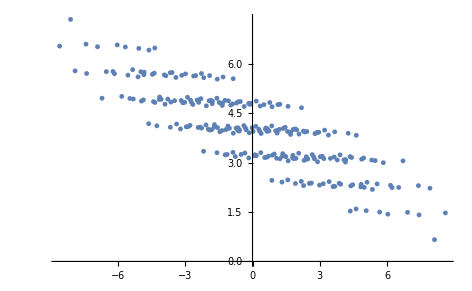

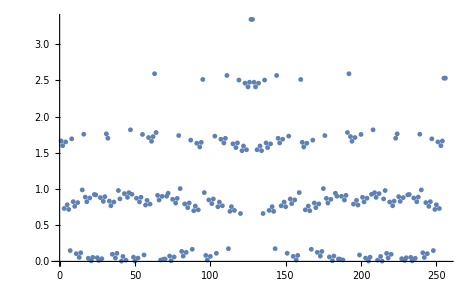

```mathematica
data = Table[
select = PadLeft[IntegerDigits[ii,2],L];

energy = Total[EsO[[YY]]]*0.5 + EsO[[XX]].select;
II=DiagonalMatrix[select];
cmat = CmatO+Transpose[gMatO].II.Conjugate[ gMatO]-Transpose[Conjugate[hMatO]].II. hMatO;
(*cmat = CmatO+Transpose[gMatO].II.Conjugate[ gMatO]-Transpose[Conjugate[gMatO]].II. hMatO;*)
(*cmat = CmatO+Transpose[hMatO].II.Conjugate[ hMatO]-Transpose[Conjugate[hMatO]].II. gMatO;*)
part=Tr[cmat];
{energy,part}
,{ii,1,2^L}];
ListPlot[data]
data2 = Table[
select = PadLeft[IntegerDigits[ii,2],L];

energy = Total[EsO[[YY]]]*0.5 + EsO[[XX]].select;
II=DiagonalMatrix[select];
cmat = CmatO+Transpose[gMatO].II.Conjugate[ gMatO]-Transpose[Conjugate[hMatO]].II. hMatO;
(*cmat = CmatO+Transpose[hMatO].II.Conjugate[ hMatO]-Transpose[Conjugate[hMatO]].II. gMatO;*)
part=Abs[Tr[cmat]-L/2];
{ii,part}
,{ii,1,2^L}];
ListPlot[data2]
```

```mathematica
min = Ordering[data2[[All,2]], All, Greater]//Reverse

PadLeft[IntegerDigits[195,2],L]
```

{214,41,50,205,234,21,74,181,26,229,211,44,157,98,67,188,69,186,70,185,28,227,19,236,203,52,218,37,25,230,13,242,22,233,49,206,179,76,42,213,100,155,82,173,73,182,97,158,56,199,35,220,11,244,38,217,104,151,14,241,84,171,81,174,7,248,88,167,112,143,120,135,113,142,89,166,116,139,92,163,6,249,3,252,85,170,105,150,114,141,10,245,90,165,108,147,34,221,57,198,5,250,60,195,83,172,101,154,77,178,86,169,12,243,106,149,36,219,53,202,18,237,9,246,29,226,33,222,58,197,66,189,99,156,75,180,102,153,40,215,78,177,51,204,20,235,27,228,45,210,54,201,17,238,30,225,68,187,71,184,65,190,24,231,23,232,48,207,43,212,72,183,46,209,96,159,39,216,15,240,80,175,121,134,124,131,117,138,93,162,122,133,2,253,115,140,91,164,109,146,118,137,94,161,4,251,61,194,1,254,87,168,107,148,8,247,110,145,32,223,59,196,62,193,103,152,79,176,55,200,16,239,31,224,64,191,47,208,125,130,123,132,126,129,119,136,95,160,255,256,111,144,63,192,127,128}

{1,1,0,0,0,0,1,1}

```mathematica
bigham=0.5(+Sum[AmatO[[i,j]]*Fc[+1,i,L].Fc[-1,j,L],{i,1,L},{j,1,L}]
+Sum[-Conjugate[AmatO[[i,j]]]*Fc[-1,i,L].Fc[+1,j,L],{i,1,L},{j,1,L}]
+Sum[BmatO[[i,j]]*Fc[+1,i,L].Fc[+1,j,L],{i,1,L},{j,1,L}]
+Sum[-Conjugate[BmatO[[i,j]]]*Fc[-1,i,L].Fc[-1,j,L],{i,1,L},{j,1,L}]
);

{en,vec} = Eigensystem[bigham];
nord =Reverse[ Ordering[en, All,Greater]];
GSTATE=vec[[nord[[1]]]];

CMAT=Table[ GSTATE.Fc[+1,i,L].Fc[-1,j,L].Conjugate[GSTATE] ,{i,L},{j,L}];
MatrixForm[%]
data = Table[
select = PadLeft[IntegerDigits[ii,2],L];
energy = Total[EsO[[YY]]]*0.5 + EsO[[XX]].select;
energy
,{ii,1,2^L}];
data//Sort;
CmatO//MatrixForm
(*CmatO-CMAT//Chop//MatrixForm*)
Chop[Sort[data]-Sort[en]]
```

(0.617943 | -0.149526 | 0.0791762 | 0.0981706 | 0.0645913 | -0.0221193
-0.149526 | 0.117826 | -0.192769 | 0.0736223 | 0.0967973 | 0.104829
0.0791762 | -0.192769 | 0.385635 | -0.194707 | -0.208416 | -0.233353
0.0981706 | 0.0736223 | -0.194707 | 0.176314 | 0.0802408 | 0.223039
0.0645913 | 0.0967973 | -0.208416 | 0.0802408 | 0.383492 | -0.20566
-0.0221193 | 0.104829 | -0.233353 | 0.223039 | -0.20566 | 0.713392)

(0.617943 | -0.149526 | 0.0791762 | 0.0981706 | 0.0645913 | -0.0221193
-0.149526 | 0.117826 | -0.192769 | 0.0736223 | 0.0967973 | 0.104829
0.0791762 | -0.192769 | 0.385635 | -0.194707 | -0.208416 | -0.233353
0.0981706 | 0.0736223 | -0.194707 | 0.176314 | 0.0802408 | 0.223039
0.0645913 | 0.0967973 | -0.208416 | 0.0802408 | 0.383492 | -0.20566
-0.0221193 | 0.104829 | -0.233353 | 0.223039 | -0.20566 | 0.713392)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
en[[nord]]
```

{-2.58431,-2.54565,-2.21203,-2.17337,-1.70633,-1.66767,-1.59944,-1.56078,-1.33405,-1.29539,-1.22716,-1.18941,-1.1885,-1.15075,-1.08438,-1.04571,-0.817136,-0.778472,-0.721462,-0.712099,-0.682799,-0.673435,-0.349183,-0.311434,-0.310519,-0.272771,-0.206397,-0.204545,-0.167734,-0.165882,-0.0995086,-0.0608449,0.0608449,0.0995086,0.165882,0.167734,0.204545,0.206397,0.272771,0.310519,0.311434,0.349183,0.673435,0.682799,0.712099,0.721462,0.778472,0.817136,1.04571,1.08438,1.15075,1.1885,1.18941,1.22716,1.29539,1.33405,1.56078,1.59944,1.66767,1.70633,2.17337,2.21203,2.54565,2.58431}

#### Entanglement PBC

```mathematica
L=10;
{l1,l2}={1,Floor[L/2]};
{Lm1,Lm2}={-2/3.,1./5000.};
ZD=0.0;
"===========================================================================";
AmatP=SparseArray[{Band[{1,1}]->-Lm1*Lm2+RandomReal[{-ZD,ZD},L],Band[{1,3}]->-1./2,Band[{3,1}]->-1./2,Band[{1,L-1}]->1./2,Band[{L-1,1}]->1./2,Band[{1,2}]->(Lm1+Lm2)/2,Band[{2,1}]->(Lm1+Lm2)/2,Band[{1,L}]->-(Lm1+Lm2)/2,Band[{L,1}]->-(Lm1+Lm2)/2},{L,L}];
BmatP=SparseArray[{Band[{1,1}]->0,Band[{1,3}]->-1./2,Band[{3,1}]->1./2,Band[{1,L-1}]->-1./2,Band[{L-1,1}]->1./2,Band[{1,2}]->-(Lm1+Lm2)/2,Band[{2,1}]->(Lm1+Lm2)/2,Band[{1,L}]->-(Lm1+Lm2)/2,Band[{L,1}]->(Lm1+Lm2)/2},{L,L}];
MmatP=Normal[ArrayFlatten[{{AmatP,BmatP},{-Conjugate[BmatP],-Conjugate[AmatP]}}]];
```

```mathematica
ttt=AbsoluteTime[];
VCsP=Eigenvectors[MmatP];
EsP = Diagonal[Chop[Conjugate[VCsP].MmatP.Transpose[VCsP]]];
Ord=Ordering[EsP,All,Greater];
{XX,YY}=Partition[Ord,Length[Ord]/2];
XX=Reverse[XX];
Ord=Flatten[{XX,YY}];
VCsP=VCsP[[Ord]];
{gMatP,hMatP}={VCsP[[1;;L,1;;L]],VCsP[[1;;L,L+1;;2*L]]};
(*CmatP=(Transpose[Conjugate[gMatP]]).(gMatP);*)
CmatP=(Transpose[Conjugate[hMatP]]).(hMatP);
Tr[CmatP]
(*GMatP=(Transpose[Conjugate[hMatP-gMatP]]).(hMatP+gMatP);
KMatP=(Transpose[Conjugate[hMatP+gMatP]]).(hMatP+gMatP);
KbMatP= (Transpose[Conjugate[hMatP-gMatP]]).(hMatP-gMatP);*)
Print["Time:",AbsoluteTime[]-ttt]
```

5.12091

Time:0.003001

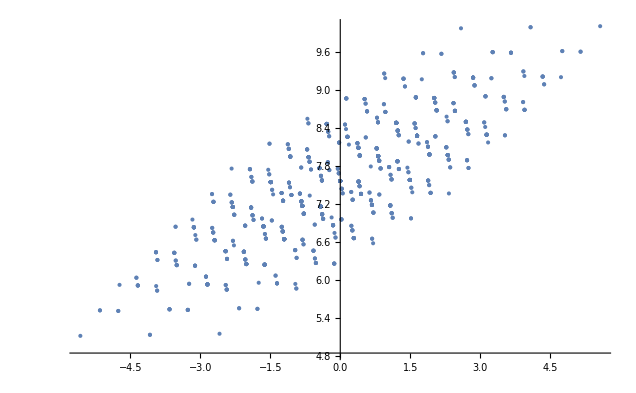

```mathematica
data = Table[
select = PadLeft[IntegerDigits[ii,2],L];
(*Print[select];*)
energy = Total[EsP[[YY]]]*0.5 + EsP[[XX]].select;
II=DiagonalMatrix[select];
cmat = CmatP+Transpose[gMatP].II.Conjugate[ gMatP]-Transpose[Conjugate[gMatP]].II. hMatP;
(*cmat = CmatP+Transpose[hMatP].II.Conjugate[ hMatP]-Transpose[Conjugate[hMatP]].II. gMatP;*)
part=Tr[cmat];
{energy,part}
,{ii,1,2^L}];
ListPlot[data]
```

```mathematica
data[[All,2]]//Max
```

10.

### G.S. to Q.C.

```mathematica
L=4;
J=1.;
AdMat =Normal[SparseArray[{Band[{1,2}]->1.,Band[{2,1}]->1,Band[{1,3}]->0,Band[{3,1}]->0},{L,L}]] ;
(*AdMat =(0.5*AA+0.5*Transpose[AA])/.AA->RandomReal[1,{L,L}];*)
{modE,modV}= Eigensystem[AdMat];
idx =  Ordering[modE,L/2];
modGS = Total[modE[[idx]]];
modMAT=modV[[idx]];

MatrixForm[modMAT]
MatrixForm[AdMat];Dimensions[modMAT];
modMAT.AdMat.Transpose[modMAT]//MatrixForm;

FullHam=Sum[-J*AdMat[[ii,jj]]*Fc[+1,ii,L].Fc[-1,jj,L],{ii,L}, {jj,L}];
{fulE,FulV}=Flatten[Eigensystem[FullHam,{2}],1]

"Checking the GS Correlation";
Transpose[modMAT].modMAT//Chop//MatrixForm
Table[FulV.Fc[-1,ii,L].Fc[+1,jj,L].FulV,{ii,L},{jj,L}]//Chop//MatrixForm
```

(0.371748 | -0.601501 | 0.601501 | -0.371748
0.601501 | -0.371748 | -0.371748 | 0.601501)

{-2.23607,{0.,0.,0.,-0.223607,0.,0.5,-0.447214,0.,0.,-0.447214,0.5,0.,-0.223607,0.,0.,0.}}

(0.5 | -0.447214 | 0 | 0.223607
-0.447214 | 0.5 | -0.223607 | 0
0 | -0.223607 | 0.5 | -0.447214
0.223607 | 0 | -0.447214 | 0.5)

(0.5 | -0.447214 | 0 | 0.223607
-0.447214 | 0.5 | -0.223607 | 0
0 | -0.223607 | 0.5 | -0.447214
0.223607 | 0 | -0.447214 | 0.5)

```mathematica
wmat =Table[modMAT[[2,jj]]*modMAT[[1,ii]],{ii,L},{jj,L}];
Dimensions[wmat]
vac =Flatten[KroneckerProduct[Sequence@@Table[{1,0},{i,1,L}]]];
WMAT = -Sum[wmat[[ii,jj]]*Fc[-1,ii,L].Fc[-1,jj,L],{ii,L},{jj,L}];
WMAT.vac
MatrixForm[%];
(*MatrixExp[MatrixLog[wmat]]//MatrixForm*)
{we,wv}=Eigensystem[wmat];
we
wv.Transpose[wv]//MatrixForm
wv//MatrixForm
```

{4,4}

{0.,0.,0.,-0.223607,0.,0.5,-0.447214,0.,0.,-0.447214,0.5,0.,-0.223607,0.,0.,0.}

{1.14452×10^-9,-1.14452×10^-9,1.46151×10^-16,7.18093×10^-18}

(1. | 1. | -0.999918 | 0.99722
1. | 1. | -0.999918 | 0.99722
-0.999918 | -0.999918 | 1. | -0.997205
0.99722 | 0.99722 | -0.997205 | 1.)

(-0.371748 | 0.601501 | -0.601501 | 0.371748
-0.371748 | 0.601501 | -0.601501 | 0.371748
0.38079 | -0.593168 | 0.601828 | -0.375438
-0.376595 | 0.617987 | -0.547464 | 0.42018)

```mathematica
testmat = RandomReal[1.,{1,1,1,1,1,1}]
Dimensions[testmat]
testmat2 = ArrayReshape[testmat, {4,16}];
Dimensions[testmat2]
{u,si,v}=SingularValueDecomposition[testmat2];
Dimensions/@{u,si,v}
si//Diagonal
testmat3 = si.v;
ArrayReshape[testmat,{4,2,2,2,2}]
Dimensions[testmat3]
```

{{{{{{0.835964}}}}}}

{1,1,1,1,1,1}

{4,16}

{{4,4},{4,16},{16,16}}

{0.835964,0.,0.,0.}

{{{{{0.835964,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}},{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}}}

{4,16}

```mathematica
L=4;
vac =Flatten[KroneckerProduct[Sequence@@Table[If[OddQ[i],{1,0},{0,1}],{i,1,L}]]];
Position[vac, 1]
```

{{6}}